```mathematica
SetDirectory["E:\\work\\thesis\\论文\\nb"];
```

```mathematica
Clear["@"];
(*dd=Reap[For[i=50,i≤81,i++,
id=Import["ca_"<>ToString[i]<>".txt","Data"];
If[i==55||i==59,,Sow[id]];]];
*)
(*try  a few data first here*)
dd=Reap[
Sow[Import["ca_"<>ToString[50]<>".txt","Data"]];
Sow[Import["ca_"<>ToString[52]<>".txt","Data"]];
];
data=dd[[2]][[1]];
Length[data];
data//MatrixForm;
rd=Import["E:\\work\\thesis\\论文\\标定后的数据\\calib_50.dat","Data"];
rd1=Import["E:\\work\\thesis\\论文\\标定后的数据\\calib_51.dat","Data"];
rd//MatrixForm;
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
Dimensions[rd]

tt=Flatten[Partition[rd,{1,2}],2];
tt1=Flatten[Partition[rd1,{1,2}],2];
(*tt=Join[Table[rd[[All,{2i-1,2i}]],{i,Length[rd[[1]]]/2}],3]*)
(*x=Map[#[[1]]Cos[#[[2]]]&,Join[Table[rd[[All,{2i-1,2i}]],{i,Length[rd]/2}]]];*)
Dimensions[tt]
Dimensions[tt1]

tt//MatrixForm;
tt1//MatrixForm;


pr=data[[1]];
pr1=data[[2]];
```

{32,16}

{256,2}

{256,2}

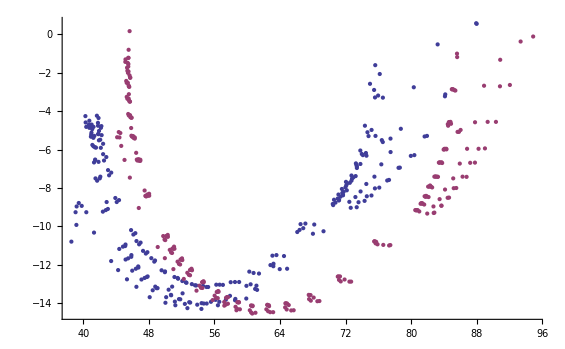

```mathematica
ListPlot[{tt,tt1}]
```

```mathematica
MatrixForm[Transpose[tt1].tt]
```

(996001. | -146089.
-127802. | 23976.)

```mathematica
ListPointPlot3D[{pr,pr1},PlotStyle->{Red,Blue},PlotStyle->PointSize[Large],Filling->Bottom]
```

-Graphics3D-

```mathematica
IdentityKernel[x_,y_]:=x.y;
k2[x_,y_]:=Diagonal[DiagonalMatrix[x]^2].Diagonal[DiagonalMatrix[y]^2];
KernelMatrix[K_,X_]:=Outer[K,X,X,1];
(*find the kernel matrix*)

K=KernelMatrix[k2,Join[rd,rd1]];
K//MatrixForm;
Dimensions[K];
```

(3.38536×10^8 | 3.218×10^8 | 3.10555×10^8 | 3.01903×10^8 | 2.93424×10^8 | 2.86924×10^8 | 2.79658×10^8 | 2.74958×10^8 | 2.70255×10^8 | 2.6487×10^8 | 2.34745×10^8 | 2.09684×10^8 | 1.90896×10^8 | 1.77059×10^8 | 1.65117×10^8 | 1.54456×10^8 | 1.44823×10^8 | 1.38105×10^8 | 1.33007×10^8 | 1.24392×10^8 | 1.17876×10^8 | 1.12669×10^8 | 1.0848×10^8 | 1.05111×10^8 | 9.56675×10^7 | 9.16018×10^7 | 8.96112×10^7 | 8.83973×10^7 | 8.7329×10^7 | 8.68525×10^7 | 8.69755×10^7 | 8.49871×10^7 | 4.05571×10^8 | 3.93396×10^8 | 3.85563×10^8 | 3.78778×10^8 | 3.72126×10^8 | 3.66245×10^8 | 3.58604×10^8 | 3.53629×10^8 | 3.48269×10^8 | 3.4223×10^8 | 3.00059×10^8 | 2.65126×10^8 | 2.3849×10^8 | 2.18082×10^8 | 2.02652×10^8 | 1.89639×10^8 | 1.78922×10^8 | 1.70567×10^8 | 1.63541×10^8 | 1.53044×10^8 | 1.44834×10^8 | 1.38381×10^8 | 1.33228×10^8 | 1.29044×10^8 | 1.17452×10^8 | 1.12252×10^8 | 1.09101×10^8 | 1.07306×10^8 | 1.06503×10^8 | 1.06111×10^8 | 1.06733×10^8 | 1.05737×10^8
3.218×10^8 | 3.06221×10^8 | 2.95676×10^8 | 2.87523×10^8 | 2.79533×10^8 | 2.73415×10^8 | 2.66549×10^8 | 2.62123×10^8 | 2.57682×10^8 | 2.52581×10^8 | 2.23863×10^8 | 2.00022×10^8 | 1.82147×10^8 | 1.68906×10^8 | 1.57543×10^8 | 1.47403×10^8 | 1.38263×10^8 | 1.31861×10^8 | 1.26983×10^8 | 1.18768×10^8 | 1.12545×10^8 | 1.07581×10^8 | 1.03588×10^8 | 1.00377×10^8 | 9.13712×10^7 | 8.74846×10^7 | 8.55977×10^7 | 8.44412×10^7 | 8.34214×10^7 | 8.29616×10^7 | 8.30805×10^7 | 8.11931×10^7 | 3.86883×10^8 | 3.75327×10^8 | 3.67876×10^8 | 3.61417×10^8 | 3.55081×10^8 | 3.49482×10^8 | 3.422×10^8 | 3.37461×10^8 | 3.32354×10^8 | 3.26593×10^8 | 2.86358×10^8 | 2.53024×10^8 | 2.27606×10^8 | 2.08132×10^8 | 1.93408×10^8 | 1.80986×10^8 | 1.70755×10^8 | 1.62779×10^8 | 1.56068×10^8 | 1.46047×10^8 | 1.38209×10^8 | 1.32049×10^8 | 1.2713×10^8 | 1.23136×10^8 | 1.12074×10^8 | 1.07113×10^8 | 1.04107×10^8 | 1.02396×10^8 | 1.01634×10^8 | 1.01259×10^8 | 1.01853×10^8 | 1.00914×10^8
3.10555×10^8 | 2.95676×10^8 | 2.85573×10^8 | 2.77743×10^8 | 2.70067×10^8 | 2.64195×10^8 | 2.57591×10^8 | 2.53341×10^8 | 2.49071×10^8 | 2.44157×10^8 | 2.16409×10^8 | 1.93396×10^8 | 1.7614×10^8 | 1.63323×10^8 | 1.52352×10^8 | 1.42564×10^8 | 1.3375×10^8 | 1.27564×10^8 | 1.22842×10^8 | 1.14901×10^8 | 1.08881×10^8 | 1.04082×10^8 | 1.00222×10^8 | 9.71182×10^7 | 8.84068×10^7 | 8.46423×10^7 | 8.28213×10^7 | 8.17029×10^7 | 8.07159×10^7 | 8.02686×10^7 | 8.0384×10^7 | 7.85644×10^7 | 3.74023×10^8 | 3.62878×10^8 | 3.55685×10^8 | 3.49451×10^8 | 3.43332×10^8 | 3.37926×10^8 | 3.3089×10^8 | 3.26312×10^8 | 3.21381×10^8 | 3.15811×10^8 | 2.76917×10^8 | 2.44692×10^8 | 2.20119×10^8 | 2.0129×10^8 | 1.87054×10^8 | 1.75041×10^8 | 1.65144×10^8 | 1.5743×10^8 | 1.50937×10^8 | 1.41243×10^8 | 1.3366×10^8 | 1.277×10^8 | 1.22942×10^8 | 1.19077×10^8 | 1.08373×10^8 | 1.03573×10^8 | 1.00666×10^8 | 9.9011×10^7 | 9.82751×10^7 | 9.79125×10^7 | 9.84857×10^7 | 9.75846×10^7
3.01903×10^8 | 2.87523×10^8 | 2.77743×10^8 | 2.70155×10^8 | 2.62714×10^8 | 2.57024×10^8 | 2.50616×10^8 | 2.46494×10^8 | 2.42352×10^8 | 2.37581×10^8 | 2.1059×10^8 | 1.88213×10^8 | 1.7143×10^8 | 1.58951×10^8 | 1.48283×10^8 | 1.38768×10^8 | 1.30203×10^8 | 1.24186×10^8 | 1.19587×10^8 | 1.11861×10^8 | 1.06001×10^8 | 1.01331×10^8 | 9.75746×10^7 | 9.45532×10^7 | 8.60728×10^7 | 8.24062×10^7 | 8.06323×10^7 | 7.95438×10^7 | 7.85829×10^7 | 7.81459×10^7 | 7.8258×10^7 | 7.64908×10^7 | 3.63978×10^8 | 3.53144×10^8 | 3.4615×10^8 | 3.40089×10^8 | 3.34136×10^8 | 3.28879×10^8 | 3.22035×10^8 | 3.17582×10^8 | 3.12786×10^8 | 3.07366×10^8 | 2.69519×10^8 | 2.38162×10^8 | 2.1425×10^8 | 1.95926×10^8 | 1.82071×10^8 | 1.70379×10^8 | 1.60745×10^8 | 1.53235×10^8 | 1.46913×10^8 | 1.37476×10^8 | 1.30094×10^8 | 1.24292×10^8 | 1.19659×10^8 | 1.15896×10^8 | 1.05474×10^8 | 1.008×10^8 | 9.79689×10^7 | 9.63582×10^7 | 9.56425×10^7 | 9.5289×10^7 | 9.58465×10^7 | 9.49731×10^7
2.93424×10^8 | 2.79533×10^8 | 2.70067×10^8 | 2.62714×10^8 | 2.55507×10^8 | 2.49995×10^8 | 2.43777×10^8 | 2.3978×10^8 | 2.35763×10^8 | 2.31132×10^8 | 2.04879×10^8 | 1.83126×10^8 | 1.66809×10^8 | 1.54656×10^8 | 1.44287×10^8 | 1.3504×10^8 | 1.26726×10^8 | 1.20872×10^8 | 1.16392×10^8 | 1.08876×10^8 | 1.03172×10^8 | 9.86282×10^7 | 9.49738×10^7 | 9.20336×10^7 | 8.37815×10^7 | 8.02113×10^7 | 7.84832×10^7 | 7.74234×10^7 | 7.64885×10^7 | 7.60615×10^7 | 7.61707×10^7 | 7.44547×10^7 | 3.54191×10^8 | 3.43645×10^8 | 3.36838×10^8 | 3.3094×10^8 | 3.25148×10^8 | 3.20032×10^8 | 3.13373×10^8 | 3.0904×10^8 | 3.04374×10^8 | 2.99099×10^8 | 2.62274×10^8 | 2.31764×10^8 | 2.08496×10^8 | 1.90665×10^8 | 1.77182×10^8 | 1.65803×10^8 | 1.56426×10^8 | 1.49117×10^8 | 1.42963×10^8 | 1.33778×10^8 | 1.26592×10^8 | 1.20945×10^8 | 1.16436×10^8 | 1.12773×10^8 | 1.02628×10^8 | 9.80785×10^7 | 9.53239×10^7 | 9.37565×10^7 | 9.30607×10^7 | 9.27163×10^7 | 9.32588×10^7 | 9.24118×10^7
2.86924×10^8 | 2.73415×10^8 | 2.64195×10^8 | 2.57024×10^8 | 2.49995×10^8 | 2.44622×10^8 | 2.38552×10^8 | 2.34654×10^8 | 2.30734×10^8 | 2.26211×10^8 | 2.00523×10^8 | 1.79249×10^8 | 1.63291×10^8 | 1.51387×10^8 | 1.41246×10^8 | 1.32204×10^8 | 1.24078×10^8 | 1.18351×10^8 | 1.13962×10^8 | 1.06605×10^8 | 1.0102×10^8 | 9.65727×10^7 | 9.29958×10^7 | 9.01177×10^7 | 8.20382×10^7 | 7.85399×10^7 | 7.68491×10^7 | 7.5811×10^7 | 7.48957×10^7 | 7.44762×10^7 | 7.45832×10^7 | 7.29059×10^7 | 3.4673×10^8 | 3.36405×10^8 | 3.29739×10^8 | 3.23965×10^8 | 3.18295×10^8 | 3.13288×10^8 | 3.06769×10^8 | 3.02528×10^8 | 2.97961×10^8 | 2.92796×10^8 | 2.56752×10^8 | 2.26889×10^8 | 2.04113×10^8 | 1.86658×10^8 | 1.73459×10^8 | 1.62319×10^8 | 1.53138×10^8 | 1.45981×10^8 | 1.39955×10^8 | 1.30961×10^8 | 1.23925×10^8 | 1.18395×10^8 | 1.1398×10^8 | 1.10393×10^8 | 1.00459×10^8 | 9.60033×10^7 | 9.33062×10^7 | 9.17716×10^7 | 9.10906×10^7 | 9.07532×10^7 | 9.12841×10^7 | 9.04571×10^7
2.79658×10^8 | 2.66549×10^8 | 2.57591×10^8 | 2.50616×10^8 | 2.43777×10^8 | 2.38552×10^8 | 2.32645×10^8 | 2.28854×10^8 | 2.25039×10^8 | 2.20634×10^8 | 1.95585×10^8 | 1.74848×10^8 | 1.59291×10^8 | 1.47676×10^8 | 1.37788×10^8 | 1.28974×10^8 | 1.21055×10^8 | 1.1547×10^8 | 1.11188×10^8 | 1.04013×10^8 | 9.85644×10^7 | 9.4227×10^7 | 9.07385×10^7 | 8.79313×10^7 | 8.00486×10^7 | 7.66338×10^7 | 7.49857×10^7 | 7.39732×10^7 | 7.308×10^7 | 7.26699×10^7 | 7.27743×10^7 | 7.11402×10^7 | 3.38179×10^8 | 3.28122×10^8 | 3.21627×10^8 | 3.16×10^8 | 3.10473×10^8 | 3.05593×10^8 | 2.99237×10^8 | 2.95103×10^8 | 2.9065×10^8 | 2.85613×10^8 | 2.50459×10^8 | 2.21332×10^8 | 1.99118×10^8 | 1.82093×10^8 | 1.69218×10^8 | 1.58351×10^8 | 1.49393×10^8 | 1.42411×10^8 | 1.36532×10^8 | 1.27757×10^8 | 1.20893×10^8 | 1.15497×10^8 | 1.11189×10^8 | 1.07689×10^8 | 9.79959×10^7 | 9.36485×10^7 | 9.1017×10^7 | 8.952×10^7 | 8.88562×10^7 | 8.85268×10^7 | 8.90443×10^7 | 8.82402×10^7
2.74958×10^8 | 2.62123×10^8 | 2.53341×10^8 | 2.46494×10^8 | 2.3978×10^8 | 2.34654×10^8 | 2.28854×10^8 | 2.25135×10^8 | 2.2139×10^8 | 2.17061×10^8 | 1.92421×10^8 | 1.72034×10^8 | 1.56739×10^8 | 1.45305×10^8 | 1.35582×10^8 | 1.26914×10^8 | 1.19131×10^8 | 1.13637×10^8 | 1.09421×10^8 | 1.02363×10^8 | 9.69993×10^7 | 9.27319×10^7 | 8.92993×10^7 | 8.65374×10^7 | 7.87799×10^7 | 7.54166×10^7 | 7.37978×10^7 | 7.28011×10^7 | 7.19218×10^7 | 7.15173×10^7 | 7.16205×10^7 | 7.0014×10^7 | 3.32724×10^8 | 3.22837×10^8 | 3.1645×10^8 | 3.10917×10^8 | 3.05481×10^8 | 3.00681×10^8 | 2.9443×10^8 | 2.90363×10^8 | 2.85984×10^8 | 2.81028×10^8 | 2.46442×10^8 | 2.17787×10^8 | 1.95931×10^8 | 1.79181×10^8 | 1.66513×10^8 | 1.5582×10^8 | 1.47006×10^8 | 1.40135×10^8 | 1.34348×10^8 | 1.25714×10^8 | 1.18958×10^8 | 1.13648×10^8 | 1.09408×10^8 | 1.05963×10^8 | 9.6423×10^7 | 9.21441×10^7 | 8.95542×10^7 | 8.80808×10^7 | 8.74277×10^7 | 8.71035×10^7 | 8.76125×10^7 | 8.68227×10^7
2.70255×10^8 | 2.57682×10^8 | 2.49071×10^8 | 2.42352×10^8 | 2.35763×10^8 | 2.30734×10^8 | 2.25039×10^8 | 2.2139×10^8 | 2.17714×10^8 | 2.13462×10^8 | 1.89234×10^8 | 1.69195×10^8 | 1.5416×10^8 | 1.42911×10^8 | 1.33353×10^8 | 1.24833×10^8 | 1.17184×10^8 | 1.11782×10^8 | 1.07635×10^8 | 1.00693×10^8 | 9.5418×10^7 | 9.12213×10^7 | 8.78455×10^7 | 8.51294×10^7 | 7.74984×10^7 | 7.41883×10^7 | 7.25969×10^7 | 7.1616×10^7 | 7.07513×10^7 | 7.03527×10^7 | 7.04543×10^7 | 6.88757×10^7 | 3.27239×10^8 | 3.17517×10^8 | 3.11235×10^8 | 3.05795×10^8 | 3.00449×10^8 | 2.95729×10^8 | 2.89582×10^8 | 2.85582×10^8 | 2.81276×10^8 | 2.76402×10^8 | 2.42388×10^8 | 2.14207×10^8 | 1.92713×10^8 | 1.76239×10^8 | 1.6378×10^8 | 1.53262×10^8 | 1.44591×10^8 | 1.37833×10^8 | 1.3214×10^8 | 1.23647×10^8 | 1.17001×10^8 | 1.11777×10^8 | 1.07607×10^8 | 1.04217×10^8 | 9.48327×10^7 | 9.06231×10^7 | 8.80756×10^7 | 8.66264×10^7 | 8.59842×10^7 | 8.56651×10^7 | 8.61657×10^7 | 8.53903×10^7
2.6487×10^8 | 2.52581×10^8 | 2.44157×10^8 | 2.37581×10^8 | 2.31132×10^8 | 2.26211×10^8 | 2.20634×10^8 | 2.17061×10^8 | 2.13462×10^8 | 2.09298×10^8 | 1.85546×10^8 | 1.65905×10^8 | 1.51168×10^8 | 1.40135×10^8 | 1.30767×10^8 | 1.22417×10^8 | 1.14923×10^8 | 1.09627×10^8 | 1.05559×10^8 | 9.87527×10^7 | 9.35791×10^7 | 8.94641×10^7 | 8.6154×10^7 | 8.34905×10^7 | 7.60068×10^7 | 7.27594×10^7 | 7.11982×10^7 | 7.02358×10^7 | 6.93879×10^7 | 6.89964×10^7 | 6.90962×10^7 | 6.75496×10^7 | 3.20868×10^8 | 3.11339×10^8 | 3.05181×10^8 | 2.99849×10^8 | 2.94608×10^8 | 2.89982×10^8 | 2.83955×10^8 | 2.80034×10^8 | 2.75813×10^8 | 2.71034×10^8 | 2.37684×10^8 | 2.10053×10^8 | 1.88978×10^8 | 1.72824×10^8 | 1.60607×10^8 | 1.50294×10^8 | 1.41791×10^8 | 1.35163×10^8 | 1.2958×10^8 | 1.2125×10^8 | 1.14733×10^8 | 1.09609×10^8 | 1.05519×10^8 | 1.02195×10^8 | 9.29904×10^7 | 8.88615×10^7 | 8.6363×10^7 | 8.49417×10^7 | 8.43121×10^7 | 8.3999×10^7 | 8.44897×10^7 | 8.37306×10^7
2.34745×10^8 | 2.23863×10^8 | 2.16409×10^8 | 2.1059×10^8 | 2.04879×10^8 | 2.00523×10^8 | 1.95585×10^8 | 1.92421×10^8 | 1.89234×10^8 | 1.85546×10^8 | 1.64504×10^8 | 1.471×10^8 | 1.34038×10^8 | 1.24268×10^8 | 1.15964×10^8 | 1.08564×10^8 | 1.01917×10^8 | 9.72229×10^7 | 9.36187×10^7 | 8.75855×10^7 | 8.29988×10^7 | 7.93485×10^7 | 7.64122×10^7 | 7.40482×10^7 | 6.7404×10^7 | 6.45204×10^7 | 6.31307×10^7 | 6.22761×10^7 | 6.15236×10^7 | 6.11761×10^7 | 6.12637×10^7 | 5.98938×10^7 | 2.84422×10^8 | 2.75977×10^8 | 2.70522×10^8 | 2.65799×10^8 | 2.61156×10^8 | 2.57059×10^8 | 2.51719×10^8 | 2.48245×10^8 | 2.44506×10^8 | 2.40271×10^8 | 2.10719×10^8 | 1.86239×10^8 | 1.67564×10^8 | 1.53248×10^8 | 1.4242×10^8 | 1.33277×10^8 | 1.25738×10^8 | 1.19861×10^8 | 1.14908×10^8 | 1.07521×10^8 | 1.01739×10^8 | 9.7194×10^7 | 9.35645×10^7 | 9.06138×10^7 | 8.24437×10^7 | 7.87766×10^7 | 7.65583×10^7 | 7.52958×10^7 | 7.4736×10^7 | 7.44574×10^7 | 7.48919×10^7 | 7.4219×10^7
2.09684×10^8 | 2.00022×10^8 | 1.93396×10^8 | 1.88213×10^8 | 1.83126×10^8 | 1.79249×10^8 | 1.74848×10^8 | 1.72034×10^8 | 1.69195×10^8 | 1.65905×10^8 | 1.471×10^8 | 1.31576×10^8 | 1.19924×10^8 | 1.11181×10^8 | 1.03765×10^8 | 9.7155×10^7 | 9.12234×10^7 | 8.70254×10^7 | 8.37955×10^7 | 7.83971×10^7 | 7.42868×10^7 | 7.10194×10^7 | 6.83888×10^7 | 6.62714×10^7 | 6.03172×10^7 | 5.77256×10^7 | 5.64853×10^7 | 5.57172×10^7 | 5.50421×10^7 | 5.4729×10^7 | 5.48091×10^7 | 5.35862×10^7 | 2.54304×10^8 | 2.46762×10^8 | 2.41894×10^8 | 2.37679×10^8 | 2.33533×10^8 | 2.29876×10^8 | 2.25106×10^8 | 2.22005×10^8 | 2.18666×10^8 | 2.14882×10^8 | 1.88472×10^8 | 1.666×10^8 | 1.49912×10^8 | 1.37116×10^8 | 1.27435×10^8 | 1.1926×10^8 | 1.12516×10^8 | 1.07257×10^8 | 1.02825×10^8 | 9.62135×10^7 | 9.10364×10^7 | 8.69668×10^7 | 8.3716×10^7 | 8.10716×10^7 | 7.3749×10^7 | 7.04593×10^7 | 6.84702×10^7 | 6.73374×10^7 | 6.6835×10^7 | 6.65844×10^7 | 6.69719×10^7 | 6.63719×10^7
1.90896×10^8 | 1.82147×10^8 | 1.7614×10^8 | 1.7143×10^8 | 1.66809×10^8 | 1.63291×10^8 | 1.59291×10^8 | 1.56739×10^8 | 1.5416×10^8 | 1.51168×10^8 | 1.34038×10^8 | 1.19924×10^8 | 1.09333×10^8 | 1.01357×10^8 | 9.46063×10^7 | 8.85893×10^7 | 8.31952×10^7 | 7.93689×10^7 | 7.64184×10^7 | 7.14954×10^7 | 6.77413×10^7 | 6.47614×10^7 | 6.23598×10^7 | 6.04276×10^7 | 5.49924×10^7 | 5.26195×10^7 | 5.14938×10^7 | 5.07904×10^7 | 5.01735×10^7 | 4.98861×10^7 | 4.99612×10^7 | 4.88479×10^7 | 2.3173×10^8 | 2.2486×10^8 | 2.20429×10^8 | 2.16594×10^8 | 2.12819×10^8 | 2.0949×10^8 | 2.05147×10^8 | 2.02325×10^8 | 1.99284×10^8 | 1.95838×10^8 | 1.71782×10^8 | 1.51864×10^8 | 1.36665×10^8 | 1.25009×10^8 | 1.16187×10^8 | 1.08738×10^8 | 1.02591×10^8 | 9.77968×10^7 | 9.37554×10^7 | 8.77262×10^7 | 8.30032×10^7 | 7.92907×10^7 | 7.63245×10^7 | 7.39104×10^7 | 6.7225×10^7 | 6.42193×10^7 | 6.24024×10^7 | 6.13671×10^7 | 6.09078×10^7 | 6.06784×10^7 | 6.1031×10^7 | 6.04848×10^7
1.77059×10^8 | 1.68906×10^8 | 1.63323×10^8 | 1.58951×10^8 | 1.54656×10^8 | 1.51387×10^8 | 1.47676×10^8 | 1.45305×10^8 | 1.42911×10^8 | 1.40135×10^8 | 1.24268×10^8 | 1.11181×10^8 | 1.01357×10^8 | 9.39839×10^7 | 8.77215×10^7 | 8.21396×10^7 | 7.71236×10^7 | 7.35771×10^7 | 7.08496×10^7 | 6.62869×10^7 | 6.28104×10^7 | 6.00458×10^7 | 5.78184×10^7 | 5.60254×10^7 | 5.09786×10^7 | 4.87769×10^7 | 4.7728×10^7 | 4.70752×10^7 | 4.65028×10^7 | 4.62374×10^7 | 4.6306×10^7 | 4.52739×10^7 | 2.14653×10^8 | 2.08311×10^8 | 2.0422×10^8 | 2.00677×10^8 | 1.97187×10^8 | 1.94109×10^8 | 1.9009×10^8 | 1.8748×10^8 | 1.84667×10^8 | 1.81478×10^8 | 1.59197×10^8 | 1.40754×10^8 | 1.26678×10^8 | 1.15882×10^8 | 1.07709×10^8 | 1.00808×10^8 | 9.51118×10^7 | 9.06687×10^7 | 8.69228×10^7 | 8.13334×10^7 | 7.69538×10^7 | 7.35109×10^7 | 7.07595×10^7 | 6.85195×10^7 | 6.23156×10^7 | 5.95242×10^7 | 5.78374×10^7 | 5.68757×10^7 | 5.64486×10^7 | 5.62351×10^7 | 5.65612×10^7 | 5.60549×10^7
1.65117×10^8 | 1.57543×10^8 | 1.52352×10^8 | 1.48283×10^8 | 1.44287×10^8 | 1.41246×10^8 | 1.37788×10^8 | 1.35582×10^8 | 1.33353×10^8 | 1.30767×10^8 | 1.15964×10^8 | 1.03765×10^8 | 9.46063×10^7 | 8.77215×10^7 | 8.18829×10^7 | 7.66786×10^7 | 7.20059×10^7 | 6.86962×10^7 | 6.61475×10^7 | 6.18887×10^7 | 5.86409×10^7 | 5.60603×10^7 | 5.39801×10^7 | 5.23054×10^7 | 4.7592×10^7 | 4.55331×10^7 | 4.45531×10^7 | 4.3942×10^7 | 4.34077×10^7 | 4.3159×10^7 | 4.32236×10^7 | 4.22618×10^7 | 2.00353×10^8 | 1.94426×10^8 | 1.90605×10^8 | 1.87298×10^8 | 1.8404×10^8 | 1.81167×10^8 | 1.77417×10^8 | 1.7498×10^8 | 1.72355×10^8 | 1.69379×10^8 | 1.48589×10^8 | 1.31381×10^8 | 1.18247×10^8 | 1.08172×10^8 | 1.00544×10^8 | 9.4103×10^7 | 8.87855×10^7 | 8.46377×10^7 | 8.114×10^7 | 7.59214×10^7 | 7.18318×10^7 | 6.86167×10^7 | 6.60472×10^7 | 6.39548×10^7 | 5.81596×10^7 | 5.55513×10^7 | 5.39756×10^7 | 5.30769×10^7 | 5.26778×10^7 | 5.2478×10^7 | 5.27822×10^7 | 5.23102×10^7
1.54456×10^8 | 1.47403×10^8 | 1.42564×10^8 | 1.38768×10^8 | 1.3504×10^8 | 1.32204×10^8 | 1.28974×10^8 | 1.26914×10^8 | 1.24833×10^8 | 1.22417×10^8 | 1.08564×10^8 | 9.7155×10^7 | 8.85893×10^7 | 8.21396×10^7 | 7.66786×10^7 | 7.18119×10^7 | 6.7446×10^7 | 6.43476×10^7 | 6.19582×10^7 | 5.79707×10^7 | 5.49271×10^7 | 5.25105×10^7 | 5.05618×10^7 | 4.89927×10^7 | 4.45765×10^7 | 4.26455×10^7 | 4.17262×10^7 | 4.11529×10^7 | 4.06522×10^7 | 4.04183×10^7 | 4.04792×10^7 | 3.95803×10^7 | 1.87592×10^8 | 1.82039×10^8 | 1.78461×10^8 | 1.75366×10^8 | 1.72316×10^8 | 1.69628×10^8 | 1.66117×10^8 | 1.63837×10^8 | 1.6138×10^8 | 1.58594×10^8 | 1.39133×10^8 | 1.23027×10^8 | 1.10732×10^8 | 1.013×10^8 | 9.41592×10^7 | 8.81278×10^7 | 8.31478×10^7 | 7.92631×10^7 | 7.59868×10^7 | 7.10988×10^7 | 6.72676×10^7 | 6.42557×10^7 | 6.18482×10^7 | 5.98874×10^7 | 5.44565×10^7 | 5.20114×10^7 | 5.05347×10^7 | 4.96923×10^7 | 4.93182×10^7 | 4.91307×10^7 | 4.94153×10^7 | 4.89741×10^7
1.44823×10^8 | 1.38263×10^8 | 1.3375×10^8 | 1.30203×10^8 | 1.26726×10^8 | 1.24078×10^8 | 1.21055×10^8 | 1.19131×10^8 | 1.17184×10^8 | 1.14923×10^8 | 1.01917×10^8 | 9.12234×10^7 | 8.31952×10^7 | 7.71236×10^7 | 7.20059×10^7 | 6.7446×10^7 | 6.33668×10^7 | 6.04579×10^7 | 5.82058×10^7 | 5.44608×10^7 | 5.15971×10^7 | 4.93286×10^7 | 4.74978×10^7 | 4.60238×10^7 | 4.18774×10^7 | 4.00605×10^7 | 3.91974×10^7 | 3.86573×10^7 | 3.81871×10^7 | 3.79656×10^7 | 3.8024×10^7 | 3.71821×10^7 | 1.7623×10^8 | 1.70997×10^8 | 1.67629×10^8 | 1.64717×10^8 | 1.6185×10^8 | 1.59323×10^8 | 1.56024×10^8 | 1.53881×10^8 | 1.51572×10^8 | 1.48954×10^8 | 1.30678×10^8 | 1.15551×10^8 | 1.04005×10^8 | 9.5146×10^7 | 8.84377×10^7 | 8.27722×10^7 | 7.80934×10^7 | 7.44439×10^7 | 7.13656×10^7 | 6.67738×10^7 | 6.31742×10^7 | 6.03447×10^7 | 5.80829×10^7 | 5.62405×10^7 | 5.11376×10^7 | 4.88402×10^7 | 4.74529×10^7 | 4.66615×10^7 | 4.63103×10^7 | 4.61341×10^7 | 4.64014×10^7 | 4.59882×10^7
1.38105×10^8 | 1.31861×10^8 | 1.27564×10^8 | 1.24186×10^8 | 1.20872×10^8 | 1.18351×10^8 | 1.1547×10^8 | 1.13637×10^8 | 1.11782×10^8 | 1.09627×10^8 | 9.72229×10^7 | 8.70254×10^7 | 7.93689×10^7 | 7.35771×10^7 | 6.86962×10^7 | 6.43476×10^7 | 6.04579×10^7 | 5.76836×10^7 | 5.55351×10^7 | 5.1963×10^7 | 4.92313×10^7 | 4.70673×10^7 | 4.53208×10^7 | 4.39147×10^7 | 3.99582×10^7 | 3.82241×10^7 | 3.74004×10^7 | 3.68847×10^7 | 3.64362×10^7 | 3.62248×10^7 | 3.62806×10^7 | 3.54779×10^7 | 1.68101×10^8 | 1.63113×10^8 | 1.59902×10^8 | 1.57126×10^8 | 1.54393×10^8 | 1.51983×10^8 | 1.48838×10^8 | 1.46794×10^8 | 1.44593×10^8 | 1.42095×10^8 | 1.24663×10^8 | 1.10235×10^8 | 9.92213×10^7 | 9.07708×10^7 | 8.43716×10^7 | 7.89669×10^7 | 7.45031×10^7 | 7.10213×10^7 | 6.80843×10^7 | 6.37035×10^7 | 6.02691×10^7 | 5.75693×10^7 | 5.54113×10^7 | 5.36533×10^7 | 4.8784×10^7 | 4.65917×10^7 | 4.52679×10^7 | 4.45128×10^7 | 4.41778×10^7 | 4.40095×10^7 | 4.42645×10^7 | 4.38708×10^7
1.33007×10^8 | 1.26983×10^8 | 1.22842×10^8 | 1.19587×10^8 | 1.16392×10^8 | 1.13962×10^8 | 1.11188×10^8 | 1.09421×10^8 | 1.07635×10^8 | 1.05559×10^8 | 9.36187×10^7 | 8.37955×10^7 | 7.64184×10^7 | 7.08496×10^7 | 6.61475×10^7 | 6.19582×10^7 | 5.82058×10^7 | 5.55351×10^7 | 5.34705×10^7 | 5.00322×10^7 | 4.74048×10^7 | 4.53209×10^7 | 4.36398×10^7 | 4.2286×10^7 | 3.84748×10^7 | 3.68057×10^7 | 3.60109×10^7 | 3.55145×10^7 | 3.50829×10^7 | 3.48801×10^7 | 3.49331×10^7 | 3.41603×10^7 | 1.61812×10^8 | 1.57018×10^8 | 1.53931×10^8 | 1.51261×10^8 | 1.48632×10^8 | 1.46313×10^8 | 1.43287×10^8 | 1.41321×10^8 | 1.39202×10^8 | 1.36799×10^8 | 1.20018×10^8 | 1.0613×10^8 | 9.55279×10^7 | 8.73931×10^7 | 8.12332×10^7 | 7.60299×10^7 | 7.17325×10^7 | 6.83804×10^7 | 6.55527×10^7 | 6.13347×10^7 | 5.80281×10^7 | 5.54286×10^7 | 5.33507×10^7 | 5.16578×10^7 | 4.69691×10^7 | 4.48578×10^7 | 4.3583×10^7 | 4.28559×10^7 | 4.25332×10^7 | 4.23711×10^7 | 4.26164×10^7 | 4.22376×10^7
1.24392×10^8 | 1.18768×10^8 | 1.14901×10^8 | 1.11861×10^8 | 1.08876×10^8 | 1.06605×10^8 | 1.04013×10^8 | 1.02363×10^8 | 1.00693×10^8 | 9.87527×10^7 | 8.75855×10^7 | 7.83971×10^7 | 7.14954×10^7 | 6.62869×10^7 | 6.18887×10^7 | 5.79707×10^7 | 5.44608×10^7 | 5.1963×10^7 | 5.00322×10^7 | 4.68164×10^7 | 4.43591×10^7 | 4.24096×10^7 | 4.08372×10^7 | 3.95706×10^7 | 3.60042×10^7 | 3.44423×10^7 | 3.36973×10^7 | 3.32327×10^7 | 3.2829×10^7 | 3.26392×10^7 | 3.26887×10^7 | 3.19663×10^7 | 1.51374×10^8 | 1.46892×10^8 | 1.44004×10^8 | 1.41508×10^8 | 1.39049×10^8 | 1.36881×10^8 | 1.3405×10^8 | 1.32211×10^8 | 1.3023×10^8 | 1.27982×10^8 | 1.12284×10^8 | 9.92931×10^7 | 8.93748×10^7 | 8.17646×10^7 | 7.60019×10^7 | 7.11336×10^7 | 6.71127×10^7 | 6.39764×10^7 | 6.13304×10^7 | 5.73838×10^7 | 5.42898×10^7 | 5.18575×10^7 | 4.99132×10^7 | 4.8329×10^7 | 4.39415×10^7 | 4.19657×10^7 | 4.0773×10^7 | 4.00926×10^7 | 3.97908×10^7 | 3.9639×10^7 | 3.98685×10^7 | 3.95145×10^7
1.17876×10^8 | 1.12545×10^8 | 1.08881×10^8 | 1.06001×10^8 | 1.03172×10^8 | 1.0102×10^8 | 9.85644×10^7 | 9.69993×10^7 | 9.5418×10^7 | 9.35791×10^7 | 8.29988×10^7 | 7.42868×10^7 | 6.77413×10^7 | 6.28104×10^7 | 5.86409×10^7 | 5.49271×10^7 | 5.15971×10^7 | 4.92313×10^7 | 4.74048×10^7 | 4.43591×10^7 | 4.20337×10^7 | 4.01869×10^7 | 3.86982×10^7 | 3.74988×10^7 | 3.41201×10^7 | 3.26417×10^7 | 3.19346×10^7 | 3.14947×10^7 | 3.11127×10^7 | 3.09336×10^7 | 3.09799×10^7 | 3.02954×10^7 | 1.43414×10^8 | 1.39174×10^8 | 1.3644×10^8 | 1.34077×10^8 | 1.31748×10^8 | 1.29695×10^8 | 1.27013×10^8 | 1.25271×10^8 | 1.23395×10^8 | 1.21265×10^8 | 1.0639×10^8 | 9.40794×10^7 | 8.46805×10^7 | 7.74692×10^7 | 7.20089×10^7 | 6.73957×10^7 | 6.35856×10^7 | 6.06141×10^7 | 5.81071×10^7 | 5.43678×10^7 | 5.14369×10^7 | 4.91325×10^7 | 4.72907×10^7 | 4.57901×10^7 | 4.16343×10^7 | 3.97633×10^7 | 3.86338×10^7 | 3.79897×10^7 | 3.77041×10^7 | 3.75604×10^7 | 3.77779×10^7 | 3.74429×10^7
1.12669×10^8 | 1.07581×10^8 | 1.04082×10^8 | 1.01331×10^8 | 9.86282×10^7 | 9.65727×10^7 | 9.4227×10^7 | 9.27319×10^7 | 9.12213×10^7 | 8.94641×10^7 | 7.93485×10^7 | 7.10194×10^7 | 6.47614×10^7 | 6.00458×10^7 | 5.60603×10^7 | 5.25105×10^7 | 4.93286×10^7 | 4.70673×10^7 | 4.53209×10^7 | 4.24096×10^7 | 4.01869×10^7 | 3.84219×10^7 | 3.69992×10^7 | 3.58531×10^7 | 3.2624×10^7 | 3.1211×10^7 | 3.0535×10^7 | 3.01142×10^7 | 2.97495×10^7 | 2.95783×10^7 | 2.96227×10^7 | 2.89686×10^7 | 1.37119×10^8 | 1.33065×10^8 | 1.3045×10^8 | 1.2819×10^8 | 1.25963×10^8 | 1.24×10^8 | 1.21436×10^8 | 1.1977×10^8 | 1.17975×10^8 | 1.15939×10^8 | 1.01716×10^8 | 8.99443×10^7 | 8.09569×10^7 | 7.40615×10^7 | 6.88407×10^7 | 6.44297×10^7 | 6.07868×10^7 | 5.79458×10^7 | 5.55489×10^7 | 5.19741×10^7 | 4.91723×10^7 | 4.69694×10^7 | 4.5209×10^7 | 4.37746×10^7 | 3.98027×10^7 | 3.80148×10^7 | 3.69355×10^7 | 3.632×10^7 | 3.60473×10^7 | 3.591×10^7 | 3.61181×10^7 | 3.57979×10^7
1.0848×10^8 | 1.03588×10^8 | 1.00222×10^8 | 9.75746×10^7 | 9.49738×10^7 | 9.29958×10^7 | 9.07385×10^7 | 8.92993×10^7 | 8.78455×10^7 | 8.6154×10^7 | 7.64122×10^7 | 6.83888×10^7 | 6.23598×10^7 | 5.78184×10^7 | 5.39801×10^7 | 5.05618×10^7 | 4.74978×10^7 | 4.53208×10^7 | 4.36398×10^7 | 4.08372×10^7 | 3.86982×10^7 | 3.69992×10^7 | 3.56302×10^7 | 3.45273×10^7 | 3.14195×10^7 | 3.00603×10^7 | 2.94093×10^7 | 2.90046×10^7 | 2.86537×10^7 | 2.8489×10^7 | 2.85316×10^7 | 2.79019×10^7 | 1.32046×10^8 | 1.28144×10^8 | 1.25626×10^8 | 1.2345×10^8 | 1.21305×10^8 | 1.19414×10^8 | 1.16945×10^8 | 1.15341×10^8 | 1.13613×10^8 | 1.11651×10^8 | 9.79528×10^7 | 8.66136×10^7 | 7.79567×10^7 | 7.13153×10^7 | 6.62873×10^7 | 6.2039×10^7 | 5.85306×10^7 | 5.57949×10^7 | 5.34868×10^7 | 5.00447×10^7 | 4.73472×10^7 | 4.52263×10^7 | 4.35317×10^7 | 4.21511×10^7 | 3.83281×10^7 | 3.66079×10^7 | 3.55693×10^7 | 3.49773×10^7 | 3.47151×10^7 | 3.45832×10^7 | 3.47836×10^7 | 3.44758×10^7
1.05111×10^8 | 1.00377×10^8 | 9.71182×10^7 | 9.45532×10^7 | 9.20336×10^7 | 9.01177×10^7 | 8.79313×10^7 | 8.65374×10^7 | 8.51294×10^7 | 8.34905×10^7 | 7.40482×10^7 | 6.62714×10^7 | 6.04276×10^7 | 5.60254×10^7 | 5.23054×10^7 | 4.89927×10^7 | 4.60238×10^7 | 4.39147×10^7 | 4.2286×10^7 | 3.95706×10^7 | 3.74988×10^7 | 3.58531×10^7 | 3.45273×10^7 | 3.34595×10^7 | 3.04497×10^7 | 2.91335×10^7 | 2.85037×10^7 | 2.81117×10^7 | 2.77721×10^7 | 2.76128×10^7 | 2.76541×10^7 | 2.7044×10^7 | 1.27962×10^8 | 1.24185×10^8 | 1.21745×10^8 | 1.19636×10^8 | 1.17558×10^8 | 1.15725×10^8 | 1.13333×10^8 | 1.11778×10^8 | 1.10103×10^8 | 1.08202×10^8 | 9.49245×10^7 | 8.39326×10^7 | 7.55412×10^7 | 6.9104×10^7 | 6.4231×10^7 | 6.01135×10^7 | 5.67136×10^7 | 5.40626×10^7 | 5.18262×10^7 | 4.8491×10^7 | 4.58777×10^7 | 4.3823×10^7 | 4.21816×10^7 | 4.08443×10^7 | 3.71418×10^7 | 3.54763×10^7 | 3.44707×10^7 | 3.38977×10^7 | 3.36442×10^7 | 3.35166×10^7 | 3.3711×10^7 | 3.34131×10^7
9.56675×10^7 | 9.13712×10^7 | 8.84068×10^7 | 8.60728×10^7 | 8.37815×10^7 | 8.20382×10^7 | 8.00486×10^7 | 7.87799×10^7 | 7.74984×10^7 | 7.60068×10^7 | 6.7404×10^7 | 6.03172×10^7 | 5.49924×10^7 | 5.09786×10^7 | 4.7592×10^7 | 4.45765×10^7 | 4.18774×10^7 | 3.99582×10^7 | 3.84748×10^7 | 3.60042×10^7 | 3.41201×10^7 | 3.2624×10^7 | 3.14195×10^7 | 3.04497×10^7 | 2.7717×10^7 | 2.65231×10^7 | 2.59516×10^7 | 2.55962×10^7 | 2.5288×10^7 | 2.51434×10^7 | 2.51811×10^7 | 2.46259×10^7 | 1.16521×10^8 | 1.13083×10^8 | 1.10859×10^8 | 1.08936×10^8 | 1.07042×10^8 | 1.05372×10^8 | 1.03192×10^8 | 1.01775×10^8 | 1.00249×10^8 | 9.85163×10^7 | 8.64187×10^7 | 7.63999×10^7 | 6.87528×10^7 | 6.28882×10^7 | 5.84501×10^7 | 5.47001×10^7 | 5.16047×10^7 | 4.91919×10^7 | 4.7157×10^7 | 4.41225×10^7 | 4.1746×10^7 | 3.98775×10^7 | 3.83856×10^7 | 3.71707×10^7 | 3.38074×10^7 | 3.22966×10^7 | 3.13838×10^7 | 3.08644×10^7 | 3.06351×10^7 | 3.05197×10^7 | 3.06971×10^7 | 3.04267×10^7
9.16018×10^7 | 8.74846×10^7 | 8.46423×10^7 | 8.24062×10^7 | 8.02113×10^7 | 7.85399×10^7 | 7.66338×10^7 | 7.54166×10^7 | 7.41883×10^7 | 7.27594×10^7 | 6.45204×10^7 | 5.77256×10^7 | 5.26195×10^7 | 4.87769×10^7 | 4.55331×10^7 | 4.26455×10^7 | 4.00605×10^7 | 3.82241×10^7 | 3.68057×10^7 | 3.44423×10^7 | 3.26417×10^7 | 3.1211×10^7 | 3.00603×10^7 | 2.91335×10^7 | 2.65231×10^7 | 2.53855×10^7 | 2.48381×10^7 | 2.44999×10^7 | 2.42055×10^7 | 2.40677×10^7 | 2.41032×10^7 | 2.35718×10^7 | 1.11543×10^8 | 1.08255×10^8 | 1.06125×10^8 | 1.04283×10^8 | 1.02469×10^8 | 1.00869×10^8 | 9.87809×10^7 | 9.74228×10^7 | 9.59617×10^7 | 9.43021×10^7 | 8.27153×10^7 | 7.31168×10^7 | 6.57917×10^7 | 6.0175×10^7 | 5.5926×10^7 | 5.23357×10^7 | 4.93731×10^7 | 4.70643×10^7 | 4.51176×10^7 | 4.22147×10^7 | 3.99422×10^7 | 3.81555×10^7 | 3.67293×10^7 | 3.55686×10^7 | 3.23554×10^7 | 3.09134×10^7 | 3.00419×10^7 | 2.95464×10^7 | 2.9328×10^7 | 2.9218×10^7 | 2.93881×10^7 | 2.91298×10^7
8.96112×10^7 | 8.55977×10^7 | 8.28213×10^7 | 8.06323×10^7 | 7.84832×10^7 | 7.68491×10^7 | 7.49857×10^7 | 7.37978×10^7 | 7.25969×10^7 | 7.11982×10^7 | 6.31307×10^7 | 5.64853×10^7 | 5.14938×10^7 | 4.7728×10^7 | 4.45531×10^7 | 4.17262×10^7 | 3.91974×10^7 | 3.74004×10^7 | 3.60109×10^7 | 3.36973×10^7 | 3.19346×10^7 | 3.0535×10^7 | 2.94093×10^7 | 2.85037×10^7 | 2.59516×10^7 | 2.48381×10^7 | 2.43089×10^7 | 2.39788×10^7 | 2.36903×10^7 | 2.35555×10^7 | 2.3591×10^7 | 2.30704×10^7 | 1.09137×10^8 | 1.0593×10^8 | 1.0385×10^8 | 1.02049×10^8 | 1.00276×10^8 | 9.87106×10^7 | 9.66684×10^7 | 9.53402×10^7 | 9.3911×10^7 | 9.22875×10^7 | 8.09456×10^7 | 7.15492×10^7 | 6.43791×10^7 | 5.88822×10^7 | 5.4724×10^7 | 5.12106×10^7 | 4.8312×10^7 | 4.6053×10^7 | 4.41487×10^7 | 4.13088×10^7 | 3.90857×10^7 | 3.73381×10^7 | 3.59434×10^7 | 3.48084×10^7 | 3.16665×10^7 | 3.02571×10^7 | 2.9405×10^7 | 2.89208×10^7 | 2.87077×10^7 | 2.86004×10^7 | 2.87668×10^7 | 2.85148×10^7
8.83973×10^7 | 8.44412×10^7 | 8.17029×10^7 | 7.95438×10^7 | 7.74234×10^7 | 7.5811×10^7 | 7.39732×10^7 | 7.28011×10^7 | 7.1616×10^7 | 7.02358×10^7 | 6.22761×10^7 | 5.57172×10^7 | 5.07904×10^7 | 4.70752×10^7 | 4.3942×10^7 | 4.11529×10^7 | 3.86573×10^7 | 3.68847×10^7 | 3.55145×10^7 | 3.32327×10^7 | 3.14947×10^7 | 3.01142×10^7 | 2.90046×10^7 | 2.81117×10^7 | 2.55962×10^7 | 2.44999×10^7 | 2.39788×10^7 | 2.36551×10^7 | 2.337×10^7 | 2.32371×10^7 | 2.32718×10^7 | 2.27584×10^7 | 1.07646×10^8 | 1.04489×10^8 | 1.0244×10^8 | 1.00665×10^8 | 9.89163×10^7 | 9.73729×10^7 | 9.53587×10^7 | 9.40491×10^7 | 9.26398×10^7 | 9.10383×10^7 | 7.98482×10^7 | 7.05764×10^7 | 6.3502×10^7 | 5.80791×10^7 | 5.39773×10^7 | 5.05114×10^7 | 4.76525×10^7 | 4.54244×10^7 | 4.35464×10^7 | 4.07456×10^7 | 3.85534×10^7 | 3.68302×10^7 | 3.54549×10^7 | 3.43361×10^7 | 3.12389×10^7 | 2.98499×10^7 | 2.901×10^7 | 2.8533×10^7 | 2.83231×10^7 | 2.82175×10^7 | 2.83815×10^7 | 2.81335×10^7
8.7329×10^7 | 8.34214×10^7 | 8.07159×10^7 | 7.85829×10^7 | 7.64885×10^7 | 7.48957×10^7 | 7.308×10^7 | 7.19218×10^7 | 7.07513×10^7 | 6.93879×10^7 | 6.15236×10^7 | 5.50421×10^7 | 5.01735×10^7 | 4.65028×10^7 | 4.34077×10^7 | 4.06522×10^7 | 3.81871×10^7 | 3.64362×10^7 | 3.50829×10^7 | 3.2829×10^7 | 3.11127×10^7 | 2.97495×10^7 | 2.86537×10^7 | 2.77721×10^7 | 2.5288×10^7 | 2.42055×10^7 | 2.36903×10^7 | 2.337×10^7 | 2.30892×10^7 | 2.29581×10^7 | 2.29926×10^7 | 2.24855×10^7 | 1.06364×10^8 | 1.03241×10^8 | 1.01214×10^8 | 9.94586×10^7 | 9.77297×10^7 | 9.62039×10^7 | 9.4213×10^7 | 9.2918×10^7 | 9.15248×10^7 | 8.99419×10^7 | 7.88847×10^7 | 6.97225×10^7 | 6.27317×10^7 | 5.7373×10^7 | 5.33202×10^7 | 4.98956×10^7 | 4.70709×10^7 | 4.48697×10^7 | 4.30143×10^7 | 4.02474×10^7 | 3.80822×10^7 | 3.638×10^7 | 3.50218×10^7 | 3.39168×10^7 | 3.08584×10^7 | 2.94872×10^7 | 2.86579×10^7 | 2.8187×10^7 | 2.798×10^7 | 2.78757×10^7 | 2.8038×10^7 | 2.77928×10^7
8.68525×10^7 | 8.29616×10^7 | 8.02686×10^7 | 7.81459×10^7 | 7.60615×10^7 | 7.44762×10^7 | 7.26699×10^7 | 7.15173×10^7 | 7.03527×10^7 | 6.89964×10^7 | 6.11761×10^7 | 5.4729×10^7 | 4.98861×10^7 | 4.62374×10^7 | 4.3159×10^7 | 4.04183×10^7 | 3.79656×10^7 | 3.62248×10^7 | 3.48801×10^7 | 3.26392×10^7 | 3.09336×10^7 | 2.95783×10^7 | 2.8489×10^7 | 2.76128×10^7 | 2.51434×10^7 | 2.40677×10^7 | 2.35555×10^7 | 2.32371×10^7 | 2.29581×10^7 | 2.28282×10^7 | 2.28625×10^7 | 2.23584×10^7 | 1.05752×10^8 | 1.02649×10^8 | 1.00634×10^8 | 9.88891×10^7 | 9.71704×10^7 | 9.56535×10^7 | 9.36742×10^7 | 9.23866×10^7 | 9.10015×10^7 | 8.94278×10^7 | 7.8433×10^7 | 6.93222×10^7 | 6.23707×10^7 | 5.70423×10^7 | 5.30126×10^7 | 4.96075×10^7 | 4.67991×10^7 | 4.46107×10^7 | 4.27661×10^7 | 4.00153×10^7 | 3.78628×10^7 | 3.61706×10^7 | 3.48204×10^7 | 3.37221×10^7 | 3.0682×10^7 | 2.93192×10^7 | 2.84949×10^7 | 2.8027×10^7 | 2.78212×10^7 | 2.77176×10^7 | 2.78791×10^7 | 2.76352×10^7
8.69755×10^7 | 8.30805×10^7 | 8.0384×10^7 | 7.8258×10^7 | 7.61707×10^7 | 7.45832×10^7 | 7.27743×10^7 | 7.16205×10^7 | 7.04543×10^7 | 6.90962×10^7 | 6.12637×10^7 | 5.48091×10^7 | 4.99612×10^7 | 4.6306×10^7 | 4.32236×10^7 | 4.04792×10^7 | 3.8024×10^7 | 3.62806×10^7 | 3.49331×10^7 | 3.26887×10^7 | 3.09799×10^7 | 2.96227×10^7 | 2.85316×10^7 | 2.76541×10^7 | 2.51811×10^7 | 2.41032×10^7 | 2.3591×10^7 | 2.32718×10^7 | 2.29926×10^7 | 2.28625×10^7 | 2.28974×10^7 | 2.23927×10^7 | 1.05902×10^8 | 1.02796×10^8 | 1.00779×10^8 | 9.90316×10^7 | 9.73108×10^7 | 9.57921×10^7 | 9.38103×10^7 | 9.25211×10^7 | 9.11342×10^7 | 8.95584×10^7 | 7.85478×10^7 | 6.9424×10^7 | 6.24626×10^7 | 5.71266×10^7 | 5.30911×10^7 | 4.96811×10^7 | 4.68687×10^7 | 4.46771×10^7 | 4.28299×10^7 | 4.00751×10^7 | 3.79194×10^7 | 3.62247×10^7 | 3.48725×10^7 | 3.37725×10^7 | 3.07277×10^7 | 2.93628×10^7 | 2.85373×10^7 | 2.80686×10^7 | 2.78626×10^7 | 2.77588×10^7 | 2.79205×10^7 | 2.76763×10^7
8.49871×10^7 | 8.11931×10^7 | 7.85644×10^7 | 7.64908×10^7 | 7.44547×10^7 | 7.29059×10^7 | 7.11402×10^7 | 7.0014×10^7 | 6.88757×10^7 | 6.75496×10^7 | 5.98938×10^7 | 5.35862×10^7 | 4.88479×10^7 | 4.52739×10^7 | 4.22618×10^7 | 3.95803×10^7 | 3.71821×10^7 | 3.54779×10^7 | 3.41603×10^7 | 3.19663×10^7 | 3.02954×10^7 | 2.89686×10^7 | 2.79019×10^7 | 2.7044×10^7 | 2.46259×10^7 | 2.35718×10^7 | 2.30704×10^7 | 2.27584×10^7 | 2.24855×10^7 | 2.23584×10^7 | 2.23927×10^7 | 2.19005×10^7 | 1.03523×10^8 | 1.00491×10^8 | 9.85213×10^7 | 9.6815×10^7 | 9.51341×10^7 | 9.36507×10^7 | 9.17144×10^7 | 9.04548×10^7 | 8.90999×10^7 | 8.75597×10^7 | 7.67964×10^7 | 6.78776×10^7 | 6.10722×10^7 | 5.58556×10^7 | 5.19104×10^7 | 4.85765×10^7 | 4.58265×10^7 | 4.36836×10^7 | 4.18775×10^7 | 3.91838×10^7 | 3.70758×10^7 | 3.54186×10^7 | 3.40964×10^7 | 3.30207×10^7 | 3.0043×10^7 | 2.87082×10^7 | 2.79009×10^7 | 2.74427×10^7 | 2.72415×10^7 | 2.714×10^7 | 2.72979×10^7 | 2.70601×10^7
4.05571×10^8 | 3.86883×10^8 | 3.74023×10^8 | 3.63978×10^8 | 3.54191×10^8 | 3.4673×10^8 | 3.38179×10^8 | 3.32724×10^8 | 3.27239×10^8 | 3.20868×10^8 | 2.84422×10^8 | 2.54304×10^8 | 2.3173×10^8 | 2.14653×10^8 | 2.00353×10^8 | 1.87592×10^8 | 1.7623×10^8 | 1.68101×10^8 | 1.61812×10^8 | 1.51374×10^8 | 1.43414×10^8 | 1.37119×10^8 | 1.32046×10^8 | 1.27962×10^8 | 1.16521×10^8 | 1.11543×10^8 | 1.09137×10^8 | 1.07646×10^8 | 1.06364×10^8 | 1.05752×10^8 | 1.05902×10^8 | 1.03523×10^8 | 4.95402×10^8 | 4.79934×10^8 | 4.70038×10^8 | 4.61558×10^8 | 4.53288×10^8 | 4.46003×10^8 | 4.36577×10^8 | 4.30422×10^8 | 4.23812×10^8 | 4.1637×10^8 | 3.6502×10^8 | 3.2245×10^8 | 2.89995×10^8 | 2.65113×10^8 | 2.46288×10^8 | 2.30419×10^8 | 2.17322×10^8 | 2.07136×10^8 | 1.98535×10^8 | 1.85746×10^8 | 1.75749×10^8 | 1.67892×10^8 | 1.61619×10^8 | 1.56523×10^8 | 1.42442×10^8 | 1.36133×10^8 | 1.32316×10^8 | 1.30141×10^8 | 1.29172×10^8 | 1.28696×10^8 | 1.29462×10^8 | 1.28256×10^8
3.93396×10^8 | 3.75327×10^8 | 3.62878×10^8 | 3.53144×10^8 | 3.43645×10^8 | 3.36405×10^8 | 3.28122×10^8 | 3.22837×10^8 | 3.17517×10^8 | 3.11339×10^8 | 2.75977×10^8 | 2.46762×10^8 | 2.2486×10^8 | 2.08311×10^8 | 1.94426×10^8 | 1.82039×10^8 | 1.70997×10^8 | 1.63113×10^8 | 1.57018×10^8 | 1.46892×10^8 | 1.39174×10^8 | 1.33065×10^8 | 1.28144×10^8 | 1.24185×10^8 | 1.13083×10^8 | 1.08255×10^8 | 1.0593×10^8 | 1.04489×10^8 | 1.03241×10^8 | 1.02649×10^8 | 1.02796×10^8 | 1.00491×10^8 | 4.79934×10^8 | 4.65142×10^8 | 4.55648×10^8 | 4.47491×10^8 | 4.39521×10^8 | 4.32496×10^8 | 4.23392×10^8 | 4.17453×10^8 | 4.11071×10^8 | 4.03875×10^8 | 3.54086×10^8 | 3.12812×10^8 | 2.81342×10^8 | 2.5722×10^8 | 2.38972×10^8 | 2.23583×10^8 | 2.10888×10^8 | 2.01009×10^8 | 1.92672×10^8 | 1.80266×10^8 | 1.70568×10^8 | 1.62945×10^8 | 1.56861×10^8 | 1.51917×10^8 | 1.38253×10^8 | 1.32131×10^8 | 1.28427×10^8 | 1.26318×10^8 | 1.25381×10^8 | 1.24919×10^8 | 1.25659×10^8 | 1.24503×10^8
3.85563×10^8 | 3.67876×10^8 | 3.55685×10^8 | 3.4615×10^8 | 3.36838×10^8 | 3.29739×10^8 | 3.21627×10^8 | 3.1645×10^8 | 3.11235×10^8 | 3.05181×10^8 | 2.70522×10^8 | 2.41894×10^8 | 2.20429×10^8 | 2.0422×10^8 | 1.90605×10^8 | 1.78461×10^8 | 1.67629×10^8 | 1.59902×10^8 | 1.53931×10^8 | 1.44004×10^8 | 1.3644×10^8 | 1.3045×10^8 | 1.25626×10^8 | 1.21745×10^8 | 1.10859×10^8 | 1.06125×10^8 | 1.0385×10^8 | 1.0244×10^8 | 1.01214×10^8 | 1.00634×10^8 | 1.00779×10^8 | 9.85213×10^7 | 4.70038×10^8 | 4.55648×10^8 | 4.464×10^8 | 4.38442×10^8 | 4.30658×10^8 | 4.23797×10^8 | 4.14896×10^8 | 4.09093×10^8 | 4.02854×10^8 | 3.95813×10^8 | 3.47034×10^8 | 3.06599×10^8 | 2.75767×10^8 | 2.52134×10^8 | 2.34258×10^8 | 2.19179×10^8 | 2.06741×10^8 | 1.9706×10^8 | 1.88891×10^8 | 1.76732×10^8 | 1.67225×10^8 | 1.59753×10^8 | 1.53788×10^8 | 1.48942×10^8 | 1.35543×10^8 | 1.2954×10^8 | 1.25907×10^8 | 1.23839×10^8 | 1.22921×10^8 | 1.22468×10^8 | 1.23192×10^8 | 1.22064×10^8
3.78778×10^8 | 3.61417×10^8 | 3.49451×10^8 | 3.40089×10^8 | 3.3094×10^8 | 3.23965×10^8 | 3.16×10^8 | 3.10917×10^8 | 3.05795×10^8 | 2.99849×10^8 | 2.65799×10^8 | 2.37679×10^8 | 2.16594×10^8 | 2.00677×10^8 | 1.87298×10^8 | 1.75366×10^8 | 1.64717×10^8 | 1.57126×10^8 | 1.51261×10^8 | 1.41508×10^8 | 1.34077×10^8 | 1.2819×10^8 | 1.2345×10^8 | 1.19636×10^8 | 1.08936×10^8 | 1.04283×10^8 | 1.02049×10^8 | 1.00665×10^8 | 9.94586×10^7 | 9.88891×10^7 | 9.90316×10^7 | 9.6815×10^7 | 4.61558×10^8 | 4.47491×10^8 | 4.38442×10^8 | 4.30649×10^8 | 4.23021×10^8 | 4.16296×10^8 | 4.07567×10^8 | 4.01876×10^8 | 3.95759×10^8 | 3.8885×10^8 | 3.40941×10^8 | 3.0123×10^8 | 2.70949×10^8 | 2.47738×10^8 | 2.30181×10^8 | 2.15369×10^8 | 2.03152×10^8 | 1.93641×10^8 | 1.85617×10^8 | 1.73671×10^8 | 1.64329×10^8 | 1.56986×10^8 | 1.51125×10^8 | 1.46363×10^8 | 1.33193×10^8 | 1.27291×10^8 | 1.2372×10^8 | 1.21688×10^8 | 1.20786×10^8 | 1.2034×10^8 | 1.2105×10^8 | 1.19947×10^8
3.72126×10^8 | 3.55081×10^8 | 3.43332×10^8 | 3.34136×10^8 | 3.25148×10^8 | 3.18295×10^8 | 3.10473×10^8 | 3.05481×10^8 | 3.00449×10^8 | 2.94608×10^8 | 2.61156×10^8 | 2.33533×10^8 | 2.12819×10^8 | 1.97187×10^8 | 1.8404×10^8 | 1.72316×10^8 | 1.6185×10^8 | 1.54393×10^8 | 1.48632×10^8 | 1.39049×10^8 | 1.31748×10^8 | 1.25963×10^8 | 1.21305×10^8 | 1.17558×10^8 | 1.07042×10^8 | 1.02469×10^8 | 1.00276×10^8 | 9.89163×10^7 | 9.77297×10^7 | 9.71704×10^7 | 9.73108×10^7 | 9.51341×10^7 | 4.53288×10^8 | 4.39521×10^8 | 4.30658×10^8 | 4.23021×10^8 | 4.15542×10^8 | 4.08946×10^8 | 4.00381×10^8 | 3.948×10^8 | 3.88798×10^8 | 3.82017×10^8 | 3.34958×10^8 | 2.95954×10^8 | 2.66211×10^8 | 2.43412×10^8 | 2.26167×10^8 | 2.11617×10^8 | 1.99617×10^8 | 1.90272×10^8 | 1.82391×10^8 | 1.70653×10^8 | 1.61474×10^8 | 1.5426×10^8 | 1.48501×10^8 | 1.43821×10^8 | 1.30878×10^8 | 1.25077×10^8 | 1.21567×10^8 | 1.1957×10^8 | 1.18684×10^8 | 1.18246×10^8 | 1.18943×10^8 | 1.17862×10^8
3.66245×10^8 | 3.49482×10^8 | 3.37926×10^8 | 3.28879×10^8 | 3.20032×10^8 | 3.13288×10^8 | 3.05593×10^8 | 3.00681×10^8 | 2.95729×10^8 | 2.89982×10^8 | 2.57059×10^8 | 2.29876×10^8 | 2.0949×10^8 | 1.94109×10^8 | 1.81167×10^8 | 1.69628×10^8 | 1.59323×10^8 | 1.51983×10^8 | 1.46313×10^8 | 1.36881×10^8 | 1.29695×10^8 | 1.24×10^8 | 1.19414×10^8 | 1.15725×10^8 | 1.05372×10^8 | 1.00869×10^8 | 9.87106×10^7 | 9.73729×10^7 | 9.62039×10^7 | 9.56535×10^7 | 9.57921×10^7 | 9.36507×10^7 | 4.46003×10^8 | 4.32496×10^8 | 4.23797×10^8 | 4.16296×10^8 | 4.08946×10^8 | 4.02465×10^8 | 3.94045×10^8 | 3.88558×10^8 | 3.82658×10^8 | 3.7599×10^8 | 3.29682×10^8 | 2.91301×10^8 | 2.62033×10^8 | 2.39598×10^8 | 2.22628×10^8 | 2.08309×10^8 | 1.96499×10^8 | 1.87302×10^8 | 1.79546×10^8 | 1.67992×10^8 | 1.58956×10^8 | 1.51854×10^8 | 1.46185×10^8 | 1.41578×10^8 | 1.28834×10^8 | 1.23122×10^8 | 1.19666×10^8 | 1.177×10^8 | 1.16828×10^8 | 1.16396×10^8 | 1.17081×10^8 | 1.1602×10^8
3.58604×10^8 | 3.422×10^8 | 3.3089×10^8 | 3.22035×10^8 | 3.13373×10^8 | 3.06769×10^8 | 2.99237×10^8 | 2.9443×10^8 | 2.89582×10^8 | 2.83955×10^8 | 2.51719×10^8 | 2.25106×10^8 | 2.05147×10^8 | 1.9009×10^8 | 1.77417×10^8 | 1.66117×10^8 | 1.56024×10^8 | 1.48838×10^8 | 1.43287×10^8 | 1.3405×10^8 | 1.27013×10^8 | 1.21436×10^8 | 1.16945×10^8 | 1.13333×10^8 | 1.03192×10^8 | 9.87809×10^7 | 9.66684×10^7 | 9.53587×10^7 | 9.4213×10^7 | 9.36742×10^7 | 9.38103×10^7 | 9.17144×10^7 | 4.36577×10^8 | 4.23392×10^8 | 4.14896×10^8 | 4.07567×10^8 | 4.00381×10^8 | 3.94045×10^8 | 3.85808×10^8 | 3.80443×10^8 | 3.74673×10^8 | 3.68149×10^8 | 3.22814×10^8 | 2.85241×10^8 | 2.56588×10^8 | 2.34624×10^8 | 2.18012×10^8 | 2.03992×10^8 | 1.9243×10^8 | 1.83425×10^8 | 1.75831×10^8 | 1.64517×10^8 | 1.55669×10^8 | 1.48713×10^8 | 1.43162×10^8 | 1.38649×10^8 | 1.26167×10^8 | 1.20572×10^8 | 1.17187×10^8 | 1.15261×10^8 | 1.14408×10^8 | 1.13984×10^8 | 1.14654×10^8 | 1.13618×10^8
3.53629×10^8 | 3.37461×10^8 | 3.26312×10^8 | 3.17582×10^8 | 3.0904×10^8 | 3.02528×10^8 | 2.95103×10^8 | 2.90363×10^8 | 2.85582×10^8 | 2.80034×10^8 | 2.48245×10^8 | 2.22005×10^8 | 2.02325×10^8 | 1.8748×10^8 | 1.7498×10^8 | 1.63837×10^8 | 1.53881×10^8 | 1.46794×10^8 | 1.41321×10^8 | 1.32211×10^8 | 1.25271×10^8 | 1.1977×10^8 | 1.15341×10^8 | 1.11778×10^8 | 1.01775×10^8 | 9.74228×10^7 | 9.53402×10^7 | 9.40491×10^7 | 9.2918×10^7 | 9.23866×10^7 | 9.25211×10^7 | 9.04548×10^7 | 4.30422×10^8 | 4.17453×10^8 | 4.09093×10^8 | 4.01876×10^8 | 3.948×10^8 | 3.88558×10^8 | 3.80443×10^8 | 3.75158×10^8 | 3.69473×10^8 | 3.63044×10^8 | 3.18344×10^8 | 2.81299×10^8 | 2.53047×10^8 | 2.31392×10^8 | 2.15012×10^8 | 2.01188×10^8 | 1.89787×10^8 | 1.80907×10^8 | 1.73419×10^8 | 1.62261×10^8 | 1.53534×10^8 | 1.46674×10^8 | 1.41198×10^8 | 1.36748×10^8 | 1.24435×10^8 | 1.18915×10^8 | 1.15575×10^8 | 1.13675×10^8 | 1.12834×10^8 | 1.12416×10^8 | 1.13076×10^8 | 1.12056×10^8
3.48269×10^8 | 3.32354×10^8 | 3.21381×10^8 | 3.12786×10^8 | 3.04374×10^8 | 2.97961×10^8 | 2.9065×10^8 | 2.85984×10^8 | 2.81276×10^8 | 2.75813×10^8 | 2.44506×10^8 | 2.18666×10^8 | 1.99284×10^8 | 1.84667×10^8 | 1.72355×10^8 | 1.6138×10^8 | 1.51572×10^8 | 1.44593×10^8 | 1.39202×10^8 | 1.3023×10^8 | 1.23395×10^8 | 1.17975×10^8 | 1.13613×10^8 | 1.10103×10^8 | 1.00249×10^8 | 9.59617×10^7 | 9.3911×10^7 | 9.26398×10^7 | 9.15248×10^7 | 9.10015×10^7 | 9.11342×10^7 | 8.90999×10^7 | 4.23812×10^8 | 4.11071×10^8 | 4.02854×10^8 | 3.95759×10^8 | 3.88798×10^8 | 3.82658×10^8 | 3.74673×10^8 | 3.69473×10^8 | 3.63879×10^8 | 3.57551×10^8 | 3.13533×10^8 | 2.77055×10^8 | 2.49235×10^8 | 2.2791×10^8 | 2.1178×10^8 | 1.98167×10^8 | 1.86939×10^8 | 1.78193×10^8 | 1.70818×10^8 | 1.59829×10^8 | 1.51233×10^8 | 1.44476×10^8 | 1.39082×10^8 | 1.34698×10^8 | 1.22568×10^8 | 1.1713×10^8 | 1.13839×10^8 | 1.11968×10^8 | 1.11139×10^8 | 1.10727×10^8 | 1.11377×10^8 | 1.10374×10^8
3.4223×10^8 | 3.26593×10^8 | 3.15811×10^8 | 3.07366×10^8 | 2.99099×10^8 | 2.92796×10^8 | 2.85613×10^8 | 2.81028×10^8 | 2.76402×10^8 | 2.71034×10^8 | 2.40271×10^8 | 2.14882×10^8 | 1.95838×10^8 | 1.81478×10^8 | 1.69379×10^8 | 1.58594×10^8 | 1.48954×10^8 | 1.42095×10^8 | 1.36799×10^8 | 1.27982×10^8 | 1.21265×10^8 | 1.15939×10^8 | 1.11651×10^8 | 1.08202×10^8 | 9.85163×10^7 | 9.43021×10^7 | 9.22875×10^7 | 9.10383×10^7 | 8.99419×10^7 | 8.94278×10^7 | 8.95584×10^7 | 8.75597×10^7 | 4.1637×10^8 | 4.03875×10^8 | 3.95813×10^8 | 3.8885×10^8 | 3.82017×10^8 | 3.7599×10^8 | 3.68149×10^8 | 3.63044×10^8 | 3.57551×10^8 | 3.51336×10^8 | 3.08088×10^8 | 2.7225×10^8 | 2.44917×10^8 | 2.23965×10^8 | 2.08117×10^8 | 1.94741×10^8 | 1.83709×10^8 | 1.75115×10^8 | 1.6787×10^8 | 1.57071×10^8 | 1.48623×10^8 | 1.41983×10^8 | 1.36682×10^8 | 1.32373×10^8 | 1.20451×10^8 | 1.15105×10^8 | 1.11871×10^8 | 1.10031×10^8 | 1.09216×10^8 | 1.08812×10^8 | 1.09449×10^8 | 1.08465×10^8
3.00059×10^8 | 2.86358×10^8 | 2.76917×10^8 | 2.69519×10^8 | 2.62274×10^8 | 2.56752×10^8 | 2.50459×10^8 | 2.46442×10^8 | 2.42388×10^8 | 2.37684×10^8 | 2.10719×10^8 | 1.88472×10^8 | 1.71782×10^8 | 1.59197×10^8 | 1.48589×10^8 | 1.39133×10^8 | 1.30678×10^8 | 1.24663×10^8 | 1.20018×10^8 | 1.12284×10^8 | 1.0639×10^8 | 1.01716×10^8 | 9.79528×10^7 | 9.49245×10^7 | 8.64187×10^7 | 8.27153×10^7 | 8.09456×10^7 | 7.98482×10^7 | 7.88847×10^7 | 7.8433×10^7 | 7.85478×10^7 | 7.67964×10^7 | 3.6502×10^8 | 3.54086×10^8 | 3.47034×10^8 | 3.40941×10^8 | 3.34958×10^8 | 3.29682×10^8 | 3.22814×10^8 | 3.18344×10^8 | 3.13533×10^8 | 3.08088×10^8 | 2.70182×10^8 | 2.38776×10^8 | 2.1482×10^8 | 1.96455×10^8 | 1.82562×10^8 | 1.70834×10^8 | 1.6116×10^8 | 1.53622×10^8 | 1.47266×10^8 | 1.37793×10^8 | 1.30379×10^8 | 1.24552×10^8 | 1.19899×10^8 | 1.16117×10^8 | 1.05647×10^8 | 1.0095×10^8 | 9.81092×10^7 | 9.64926×10^7 | 9.57766×10^7 | 9.54201×10^7 | 9.59784×10^7 | 9.51169×10^7
2.65126×10^8 | 2.53024×10^8 | 2.44692×10^8 | 2.38162×10^8 | 2.31764×10^8 | 2.26889×10^8 | 2.21332×10^8 | 2.17787×10^8 | 2.14207×10^8 | 2.10053×10^8 | 1.86239×10^8 | 1.666×10^8 | 1.51864×10^8 | 1.40754×10^8 | 1.31381×10^8 | 1.23027×10^8 | 1.15551×10^8 | 1.10235×10^8 | 1.0613×10^8 | 9.92931×10^7 | 9.40794×10^7 | 8.99443×10^7 | 8.66136×10^7 | 8.39326×10^7 | 7.63999×10^7 | 7.31168×10^7 | 7.15492×10^7 | 7.05764×10^7 | 6.97225×10^7 | 6.93222×10^7 | 6.9424×10^7 | 6.78776×10^7 | 3.2245×10^8 | 3.12812×10^8 | 3.06599×10^8 | 3.0123×10^8 | 2.95954×10^8 | 2.91301×10^8 | 2.85241×10^8 | 2.81299×10^8 | 2.77055×10^8 | 2.7225×10^8 | 2.38776×10^8 | 2.1105×10^8 | 1.89897×10^8 | 1.73678×10^8 | 1.61405×10^8 | 1.51044×10^8 | 1.42495×10^8 | 1.35831×10^8 | 1.30213×10^8 | 1.21836×10^8 | 1.15278×10^8 | 1.10123×10^8 | 1.06006×10^8 | 1.02657×10^8 | 9.33871×10^7 | 8.92241×10^7 | 8.67071×10^7 | 8.52738×10^7 | 8.46385×10^7 | 8.43216×10^7 | 8.48138×10^7 | 8.40534×10^7
2.3849×10^8 | 2.27606×10^8 | 2.20119×10^8 | 2.1425×10^8 | 2.08496×10^8 | 2.04113×10^8 | 1.99118×10^8 | 1.95931×10^8 | 1.92713×10^8 | 1.88978×10^8 | 1.67564×10^8 | 1.49912×10^8 | 1.36665×10^8 | 1.26678×10^8 | 1.18247×10^8 | 1.10732×10^8 | 1.04005×10^8 | 9.92213×10^7 | 9.55279×10^7 | 8.93748×10^7 | 8.46805×10^7 | 8.09569×10^7 | 7.79567×10^7 | 7.55412×10^7 | 6.87528×10^7 | 6.57917×10^7 | 6.43791×10^7 | 6.3502×10^7 | 6.27317×10^7 | 6.23707×10^7 | 6.24626×10^7 | 6.10722×10^7 | 2.89995×10^8 | 2.81342×10^8 | 2.75767×10^8 | 2.70949×10^8 | 2.66211×10^8 | 2.62033×10^8 | 2.56588×10^8 | 2.53047×10^8 | 2.49235×10^8 | 2.44917×10^8 | 2.1482×10^8 | 1.89897×10^8 | 1.7088×10^8 | 1.56297×10^8 | 1.45259×10^8 | 1.3594×10^8 | 1.28249×10^8 | 1.22253×10^8 | 1.17197×10^8 | 1.09658×10^8 | 1.03753×10^8 | 9.91119×10^7 | 9.54037×10^7 | 9.23867×10^7 | 8.40336×10^7 | 8.02795×10^7 | 7.80105×10^7 | 7.67176×10^7 | 7.6144×10^7 | 7.58577×10^7 | 7.62995×10^7 | 7.5616×10^7
2.18082×10^8 | 2.08132×10^8 | 2.0129×10^8 | 1.95926×10^8 | 1.90665×10^8 | 1.86658×10^8 | 1.82093×10^8 | 1.79181×10^8 | 1.76239×10^8 | 1.72824×10^8 | 1.53248×10^8 | 1.37116×10^8 | 1.25009×10^8 | 1.15882×10^8 | 1.08172×10^8 | 1.013×10^8 | 9.5146×10^7 | 9.07708×10^7 | 8.73931×10^7 | 8.17646×10^7 | 7.74692×10^7 | 7.40615×10^7 | 7.13153×10^7 | 6.9104×10^7 | 6.28882×10^7 | 6.0175×10^7 | 5.88822×10^7 | 5.80791×10^7 | 5.7373×10^7 | 5.70423×10^7 | 5.71266×10^7 | 5.58556×10^7 | 2.65113×10^8 | 2.5722×10^8 | 2.52134×10^8 | 2.47738×10^8 | 2.43412×10^8 | 2.39598×10^8 | 2.34624×10^8 | 2.31392×10^8 | 2.2791×10^8 | 2.23965×10^8 | 1.96455×10^8 | 1.73678×10^8 | 1.56297×10^8 | 1.42965×10^8 | 1.32875×10^8 | 1.24354×10^8 | 1.17322×10^8 | 1.11838×10^8 | 1.07213×10^8 | 1.00316×10^8 | 9.49134×10^7 | 9.06665×10^7 | 8.72726×10^7 | 8.45107×10^7 | 7.68628×10^7 | 7.34236×10^7 | 7.13454×10^7 | 7.01609×10^7 | 6.96351×10^7 | 6.93723×10^7 | 6.97755×10^7 | 6.91514×10^7
2.02652×10^8 | 1.93408×10^8 | 1.87054×10^8 | 1.82071×10^8 | 1.77182×10^8 | 1.73459×10^8 | 1.69218×10^8 | 1.66513×10^8 | 1.6378×10^8 | 1.60607×10^8 | 1.4242×10^8 | 1.27435×10^8 | 1.16187×10^8 | 1.07709×10^8 | 1.00544×10^8 | 9.41592×10^7 | 8.84377×10^7 | 8.43716×10^7 | 8.12332×10^7 | 7.60019×10^7 | 7.20089×10^7 | 6.88407×10^7 | 6.62873×10^7 | 6.4231×10^7 | 5.84501×10^7 | 5.5926×10^7 | 5.4724×10^7 | 5.39773×10^7 | 5.33202×10^7 | 5.30126×10^7 | 5.30911×10^7 | 5.19104×10^7 | 2.46288×10^8 | 2.38972×10^8 | 2.34258×10^8 | 2.30181×10^8 | 2.26167×10^8 | 2.22628×10^8 | 2.18012×10^8 | 2.15012×10^8 | 2.1178×10^8 | 2.08117×10^8 | 1.82562×10^8 | 1.61405×10^8 | 1.45259×10^8 | 1.32875×10^8 | 1.235×10^8 | 1.15584×10^8 | 1.09049×10^8 | 1.03952×10^8 | 9.96548×10^7 | 9.32445×10^7 | 8.82219×10^7 | 8.42739×10^7 | 8.11185×10^7 | 7.85502×10^7 | 7.14377×10^7 | 6.82382×10^7 | 6.63051×10^7 | 6.52029×10^7 | 6.47137×10^7 | 6.44689×10^7 | 6.48432×10^7 | 6.4264×10^7
1.89639×10^8 | 1.80986×10^8 | 1.75041×10^8 | 1.70379×10^8 | 1.65803×10^8 | 1.62319×10^8 | 1.58351×10^8 | 1.5582×10^8 | 1.53262×10^8 | 1.50294×10^8 | 1.33277×10^8 | 1.1926×10^8 | 1.08738×10^8 | 1.00808×10^8 | 9.4103×10^7 | 8.81278×10^7 | 8.27722×10^7 | 7.89669×10^7 | 7.60299×10^7 | 7.11336×10^7 | 6.73957×10^7 | 6.44297×10^7 | 6.2039×10^7 | 6.01135×10^7 | 5.47001×10^7 | 5.23357×10^7 | 5.12106×10^7 | 5.05114×10^7 | 4.98956×10^7 | 4.96075×10^7 | 4.96811×10^7 | 4.85765×10^7 | 2.30419×10^8 | 2.23583×10^8 | 2.19179×10^8 | 2.15369×10^8 | 2.11617×10^8 | 2.08309×10^8 | 2.03992×10^8 | 2.01188×10^8 | 1.98167×10^8 | 1.94741×10^8 | 1.70834×10^8 | 1.51044×10^8 | 1.3594×10^8 | 1.24354×10^8 | 1.15584×10^8 | 1.08177×10^8 | 1.02063×10^8 | 9.72934×10^7 | 9.32717×10^7 | 8.72722×10^7 | 8.25707×10^7 | 7.88752×10^7 | 7.59212×10^7 | 7.35166×10^7 | 6.68565×10^7 | 6.38594×10^7 | 6.20489×10^7 | 6.10164×10^7 | 6.05579×10^7 | 6.03285×10^7 | 6.06783×10^7 | 6.01367×10^7
1.78922×10^8 | 1.70755×10^8 | 1.65144×10^8 | 1.60745×10^8 | 1.56426×10^8 | 1.53138×10^8 | 1.49393×10^8 | 1.47006×10^8 | 1.44591×10^8 | 1.41791×10^8 | 1.25738×10^8 | 1.12516×10^8 | 1.02591×10^8 | 9.51118×10^7 | 8.87855×10^7 | 8.31478×10^7 | 7.80934×10^7 | 7.45031×10^7 | 7.17325×10^7 | 6.71127×10^7 | 6.35856×10^7 | 6.07868×10^7 | 5.85306×10^7 | 5.67136×10^7 | 5.16047×10^7 | 4.93731×10^7 | 4.8312×10^7 | 4.76525×10^7 | 4.70709×10^7 | 4.67991×10^7 | 4.68687×10^7 | 4.58265×10^7 | 2.17322×10^8 | 2.10888×10^8 | 2.06741×10^8 | 2.03152×10^8 | 1.99617×10^8 | 1.96499×10^8 | 1.9243×10^8 | 1.89787×10^8 | 1.86939×10^8 | 1.83709×10^8 | 1.6116×10^8 | 1.42495×10^8 | 1.28249×10^8 | 1.17322×10^8 | 1.09049×10^8 | 1.02063×10^8 | 9.62954×10^7 | 9.17962×10^7 | 8.80025×10^7 | 8.23425×10^7 | 7.79066×10^7 | 7.44198×10^7 | 7.16324×10^7 | 6.93634×10^7 | 6.30782×10^7 | 6.02494×10^7 | 5.85405×10^7 | 5.75659×10^7 | 5.71331×10^7 | 5.69164×10^7 | 5.72461×10^7 | 5.67356×10^7
1.70567×10^8 | 1.62779×10^8 | 1.5743×10^8 | 1.53235×10^8 | 1.49117×10^8 | 1.45981×10^8 | 1.42411×10^8 | 1.40135×10^8 | 1.37833×10^8 | 1.35163×10^8 | 1.19861×10^8 | 1.07257×10^8 | 9.77968×10^7 | 9.06687×10^7 | 8.46377×10^7 | 7.92631×10^7 | 7.44439×10^7 | 7.10213×10^7 | 6.83804×10^7 | 6.39764×10^7 | 6.06141×10^7 | 5.79458×10^7 | 5.57949×10^7 | 5.40626×10^7 | 4.91919×10^7 | 4.70643×10^7 | 4.6053×10^7 | 4.54244×10^7 | 4.48697×10^7 | 4.46107×10^7 | 4.46771×10^7 | 4.36836×10^7 | 2.07136×10^8 | 2.01009×10^8 | 1.9706×10^8 | 1.93641×10^8 | 1.90272×10^8 | 1.87302×10^8 | 1.83425×10^8 | 1.80907×10^8 | 1.78193×10^8 | 1.75115×10^8 | 1.53622×10^8 | 1.35831×10^8 | 1.22253×10^8 | 1.11838×10^8 | 1.03952×10^8 | 9.72934×10^7 | 9.17962×10^7 | 8.75075×10^7 | 8.38915×10^7 | 7.84961×10^7 | 7.42674×10^7 | 7.09435×10^7 | 6.82863×10^7 | 6.61233×10^7 | 6.01312×10^7 | 5.74341×10^7 | 5.58049×10^7 | 5.48756×10^7 | 5.4463×10^7 | 5.42564×10^7 | 5.45705×10^7 | 5.40842×10^7
1.63541×10^8 | 1.56068×10^8 | 1.50937×10^8 | 1.46913×10^8 | 1.42963×10^8 | 1.39955×10^8 | 1.36532×10^8 | 1.34348×10^8 | 1.3214×10^8 | 1.2958×10^8 | 1.14908×10^8 | 1.02825×10^8 | 9.37554×10^7 | 8.69228×10^7 | 8.114×10^7 | 7.59868×10^7 | 7.13656×10^7 | 6.80843×10^7 | 6.55527×10^7 | 6.13304×10^7 | 5.81071×10^7 | 5.55489×10^7 | 5.34868×10^7 | 5.18262×10^7 | 4.7157×10^7 | 4.51176×10^7 | 4.41487×10^7 | 4.35464×10^7 | 4.30143×10^7 | 4.27661×10^7 | 4.28299×10^7 | 4.18775×10^7 | 1.98535×10^8 | 1.92672×10^8 | 1.88891×10^8 | 1.85617×10^8 | 1.82391×10^8 | 1.79546×10^8 | 1.75831×10^8 | 1.73419×10^8 | 1.70818×10^8 | 1.6787×10^8 | 1.47266×10^8 | 1.30213×10^8 | 1.17197×10^8 | 1.07213×10^8 | 9.96548×10^7 | 9.32717×10^7 | 8.80025×10^7 | 8.38915×10^7 | 8.04257×10^7 | 7.52537×10^7 | 7.12001×10^7 | 6.80138×10^7 | 6.54666×10^7 | 6.33932×10^7 | 5.76488×10^7 | 5.50633×10^7 | 5.35013×10^7 | 5.26106×10^7 | 5.22151×10^7 | 5.2017×10^7 | 5.2318×10^7 | 5.18523×10^7
1.53044×10^8 | 1.46047×10^8 | 1.41243×10^8 | 1.37476×10^8 | 1.33778×10^8 | 1.30961×10^8 | 1.27757×10^8 | 1.25714×10^8 | 1.23647×10^8 | 1.2125×10^8 | 1.07521×10^8 | 9.62135×10^7 | 8.77262×10^7 | 8.13334×10^7 | 7.59214×10^7 | 7.10988×10^7 | 6.67738×10^7 | 6.37035×10^7 | 6.13347×10^7 | 5.73838×10^7 | 5.43678×10^7 | 5.19741×10^7 | 5.00447×10^7 | 4.8491×10^7 | 4.41225×10^7 | 4.22147×10^7 | 4.13088×10^7 | 4.07456×10^7 | 4.02474×10^7 | 4.00153×10^7 | 4.00751×10^7 | 3.91838×10^7 | 1.85746×10^8 | 1.80266×10^8 | 1.76732×10^8 | 1.73671×10^8 | 1.70653×10^8 | 1.67992×10^8 | 1.64517×10^8 | 1.62261×10^8 | 1.59829×10^8 | 1.57071×10^8 | 1.37793×10^8 | 1.21836×10^8 | 1.09658×10^8 | 1.00316×10^8 | 9.32445×10^7 | 8.72722×10^7 | 8.23425×10^7 | 7.84961×10^7 | 7.52537×10^7 | 7.04148×10^7 | 6.66221×10^7 | 6.3641×10^7 | 6.12579×10^7 | 5.9318×10^7 | 5.39435×10^7 | 5.15246×10^7 | 5.00632×10^7 | 4.92298×10^7 | 4.88599×10^7 | 4.86746×10^7 | 4.89562×10^7 | 4.85207×10^7
1.44834×10^8 | 1.38209×10^8 | 1.3366×10^8 | 1.30094×10^8 | 1.26592×10^8 | 1.23925×10^8 | 1.20893×10^8 | 1.18958×10^8 | 1.17001×10^8 | 1.14733×10^8 | 1.01739×10^8 | 9.10364×10^7 | 8.30032×10^7 | 7.69538×10^7 | 7.18318×10^7 | 6.72676×10^7 | 6.31742×10^7 | 6.02691×10^7 | 5.80281×10^7 | 5.42898×10^7 | 5.14369×10^7 | 4.91723×10^7 | 4.73472×10^7 | 4.58777×10^7 | 4.1746×10^7 | 3.99422×10^7 | 3.90857×10^7 | 3.85534×10^7 | 3.80822×10^7 | 3.78628×10^7 | 3.79194×10^7 | 3.70758×10^7 | 1.75749×10^8 | 1.70568×10^8 | 1.67225×10^8 | 1.64329×10^8 | 1.61474×10^8 | 1.58956×10^8 | 1.55669×10^8 | 1.53534×10^8 | 1.51233×10^8 | 1.48623×10^8 | 1.30379×10^8 | 1.15278×10^8 | 1.03753×10^8 | 9.49134×10^7 | 8.82219×10^7 | 8.25707×10^7 | 7.79066×10^7 | 7.42674×10^7 | 7.12001×10^7 | 6.66221×10^7 | 6.30342×10^7 | 6.02142×10^7 | 5.79599×10^7 | 5.61252×10^7 | 5.10419×10^7 | 4.87546×10^7 | 4.73724×10^7 | 4.65845×10^7 | 4.62348×10^7 | 4.60597×10^7 | 4.63262×10^7 | 4.59143×10^7
1.38381×10^8 | 1.32049×10^8 | 1.277×10^8 | 1.24292×10^8 | 1.20945×10^8 | 1.18395×10^8 | 1.15497×10^8 | 1.13648×10^8 | 1.11777×10^8 | 1.09609×10^8 | 9.7194×10^7 | 8.69668×10^7 | 7.92907×10^7 | 7.35109×10^7 | 6.86167×10^7 | 6.42557×10^7 | 6.03447×10^7 | 5.75693×10^7 | 5.54286×10^7 | 5.18575×10^7 | 4.91325×10^7 | 4.69694×10^7 | 4.52263×10^7 | 4.3823×10^7 | 3.98775×10^7 | 3.81555×10^7 | 3.73381×10^7 | 3.68302×10^7 | 3.638×10^7 | 3.61706×10^7 | 3.62247×10^7 | 3.54186×10^7 | 1.67892×10^8 | 1.62945×10^8 | 1.59753×10^8 | 1.56986×10^8 | 1.5426×10^8 | 1.51854×10^8 | 1.48713×10^8 | 1.46674×10^8 | 1.44476×10^8 | 1.41983×10^8 | 1.24552×10^8 | 1.10123×10^8 | 9.91119×10^7 | 9.06665×10^7 | 8.42739×10^7 | 7.88752×10^7 | 7.44198×10^7 | 7.09435×10^7 | 6.80138×10^7 | 6.3641×10^7 | 6.02142×10^7 | 5.75208×10^7 | 5.53679×10^7 | 5.36158×10^7 | 4.87615×10^7 | 4.65776×10^7 | 4.52578×10^7 | 4.45055×10^7 | 4.41719×10^7 | 4.40047×10^7 | 4.42594×10^7 | 4.38661×10^7
1.33228×10^8 | 1.2713×10^8 | 1.22942×10^8 | 1.19659×10^8 | 1.16436×10^8 | 1.1398×10^8 | 1.11189×10^8 | 1.09408×10^8 | 1.07607×10^8 | 1.05519×10^8 | 9.35645×10^7 | 8.3716×10^7 | 7.63245×10^7 | 7.07595×10^7 | 6.60472×10^7 | 6.18482×10^7 | 5.80829×10^7 | 5.54113×10^7 | 5.33507×10^7 | 4.99132×10^7 | 4.72907×10^7 | 4.5209×10^7 | 4.35317×10^7 | 4.21816×10^7 | 3.83856×10^7 | 3.67293×10^7 | 3.59434×10^7 | 3.54549×10^7 | 3.50218×10^7 | 3.48204×10^7 | 3.48725×10^7 | 3.40964×10^7 | 1.61619×10^8 | 1.56861×10^8 | 1.53788×10^8 | 1.51125×10^8 | 1.48501×10^8 | 1.46185×10^8 | 1.43162×10^8 | 1.41198×10^8 | 1.39082×10^8 | 1.36682×10^8 | 1.19899×10^8 | 1.06006×10^8 | 9.54037×10^7 | 8.72726×10^7 | 8.11185×10^7 | 7.59212×10^7 | 7.16324×10^7 | 6.82863×10^7 | 6.54666×10^7 | 6.12579×10^7 | 5.79599×10^7 | 5.53679×10^7 | 5.32962×10^7 | 5.16105×10^7 | 4.69399×10^7 | 4.48392×10^7 | 4.35695×10^7 | 4.28461×10^7 | 4.25253×10^7 | 4.23647×10^7 | 4.26099×10^7 | 4.22316×10^7
1.29044×10^8 | 1.23136×10^8 | 1.19077×10^8 | 1.15896×10^8 | 1.12773×10^8 | 1.10393×10^8 | 1.07689×10^8 | 1.05963×10^8 | 1.04217×10^8 | 1.02195×10^8 | 9.06138×10^7 | 8.10716×10^7 | 7.39104×10^7 | 6.85195×10^7 | 6.39548×10^7 | 5.98874×10^7 | 5.62405×10^7 | 5.36533×10^7 | 5.16578×10^7 | 4.8329×10^7 | 4.57901×10^7 | 4.37746×10^7 | 4.21511×10^7 | 4.08443×10^7 | 3.71707×10^7 | 3.55686×10^7 | 3.48084×10^7 | 3.43361×10^7 | 3.39168×10^7 | 3.37221×10^7 | 3.37725×10^7 | 3.30207×10^7 | 1.56523×10^8 | 1.51917×10^8 | 1.48942×10^8 | 1.46363×10^8 | 1.43821×10^8 | 1.41578×10^8 | 1.38649×10^8 | 1.36748×10^8 | 1.34698×10^8 | 1.32373×10^8 | 1.16117×10^8 | 1.02657×10^8 | 9.23867×10^7 | 8.45107×10^7 | 7.85502×10^7 | 7.35166×10^7 | 6.93634×10^7 | 6.61233×10^7 | 6.33932×10^7 | 5.9318×10^7 | 5.61252×10^7 | 5.36158×10^7 | 5.16105×10^7 | 4.9979×10^7 | 4.54586×10^7 | 4.34263×10^7 | 4.21976×10^7 | 4.14978×10^7 | 4.11877×10^7 | 4.10324×10^7 | 4.12701×10^7 | 4.09039×10^7
1.17452×10^8 | 1.12074×10^8 | 1.08373×10^8 | 1.05474×10^8 | 1.02628×10^8 | 1.00459×10^8 | 9.79959×10^7 | 9.6423×10^7 | 9.48327×10^7 | 9.29904×10^7 | 8.24437×10^7 | 7.3749×10^7 | 6.7225×10^7 | 6.23156×10^7 | 5.81596×10^7 | 5.44565×10^7 | 5.11376×10^7 | 4.8784×10^7 | 4.69691×10^7 | 4.39415×10^7 | 4.16343×10^7 | 3.98027×10^7 | 3.83281×10^7 | 3.71418×10^7 | 3.38074×10^7 | 3.23554×10^7 | 3.16665×10^7 | 3.12389×10^7 | 3.08584×10^7 | 3.0682×10^7 | 3.07277×10^7 | 3.0043×10^7 | 1.42442×10^8 | 1.38253×10^8 | 1.35543×10^8 | 1.33193×10^8 | 1.30878×10^8 | 1.28834×10^8 | 1.26167×10^8 | 1.24435×10^8 | 1.22568×10^8 | 1.20451×10^8 | 1.05647×10^8 | 9.33871×10^7 | 8.40336×10^7 | 7.68628×10^7 | 7.14377×10^7 | 6.68565×10^7 | 6.30782×10^7 | 6.01312×10^7 | 5.76488×10^7 | 5.39435×10^7 | 5.10419×10^7 | 4.87615×10^7 | 4.69399×10^7 | 4.54586×10^7 | 4.13552×10^7 | 3.95123×10^7 | 3.83977×10^7 | 3.77635×10^7 | 3.7483×10^7 | 3.73426×10^7 | 3.75593×10^7 | 3.72265×10^7
1.12252×10^8 | 1.07113×10^8 | 1.03573×10^8 | 1.008×10^8 | 9.80785×10^7 | 9.60033×10^7 | 9.36485×10^7 | 9.21441×10^7 | 9.06231×10^7 | 8.88615×10^7 | 7.87766×10^7 | 7.04593×10^7 | 6.42193×10^7 | 5.95242×10^7 | 5.55513×10^7 | 5.20114×10^7 | 4.88402×10^7 | 4.65917×10^7 | 4.48578×10^7 | 4.19657×10^7 | 3.97633×10^7 | 3.80148×10^7 | 3.66079×10^7 | 3.54763×10^7 | 3.22966×10^7 | 3.09134×10^7 | 3.02571×10^7 | 2.98499×10^7 | 2.94872×10^7 | 2.93192×10^7 | 2.93628×10^7 | 2.87082×10^7 | 1.36133×10^8 | 1.32131×10^8 | 1.2954×10^8 | 1.27291×10^8 | 1.25077×10^8 | 1.23122×10^8 | 1.20572×10^8 | 1.18915×10^8 | 1.1713×10^8 | 1.15105×10^8 | 1.0095×10^8 | 8.92241×10^7 | 8.02795×10^7 | 7.34236×10^7 | 6.82382×10^7 | 6.38594×10^7 | 6.02494×10^7 | 5.74341×10^7 | 5.50633×10^7 | 5.15246×10^7 | 4.87546×10^7 | 4.65776×10^7 | 4.48392×10^7 | 4.34263×10^7 | 3.95123×10^7 | 3.77563×10^7 | 3.66937×10^7 | 3.60897×10^7 | 3.58229×10^7 | 3.56895×10^7 | 3.5897×10^7 | 3.55793×10^7
1.09101×10^8 | 1.04107×10^8 | 1.00666×10^8 | 9.79689×10^7 | 9.53239×10^7 | 9.33062×10^7 | 9.1017×10^7 | 8.95542×10^7 | 8.80756×10^7 | 8.6363×10^7 | 7.65583×10^7 | 6.84702×10^7 | 6.24024×10^7 | 5.78374×10^7 | 5.39756×10^7 | 5.05347×10^7 | 4.74529×10^7 | 4.52679×10^7 | 4.3583×10^7 | 4.0773×10^7 | 3.86338×10^7 | 3.69355×10^7 | 3.55693×10^7 | 3.44707×10^7 | 3.13838×10^7 | 3.00419×10^7 | 2.9405×10^7 | 2.901×10^7 | 2.86579×10^7 | 2.84949×10^7 | 2.85373×10^7 | 2.79009×10^7 | 1.32316×10^8 | 1.28427×10^8 | 1.25907×10^8 | 1.2372×10^8 | 1.21567×10^8 | 1.19666×10^8 | 1.17187×10^8 | 1.15575×10^8 | 1.13839×10^8 | 1.11871×10^8 | 9.81092×10^7 | 8.67071×10^7 | 7.80105×10^7 | 7.13454×10^7 | 6.63051×10^7 | 6.20489×10^7 | 5.85405×10^7 | 5.58049×10^7 | 5.35013×10^7 | 5.00632×10^7 | 4.73724×10^7 | 4.52578×10^7 | 4.35695×10^7 | 4.21976×10^7 | 3.83977×10^7 | 3.66937×10^7 | 3.56624×10^7 | 3.50764×10^7 | 3.48178×10^7 | 3.46885×10^7 | 3.48904×10^7 | 3.45819×10^7
1.07306×10^8 | 1.02396×10^8 | 9.9011×10^7 | 9.63582×10^7 | 9.37565×10^7 | 9.17716×10^7 | 8.952×10^7 | 8.80808×10^7 | 8.66264×10^7 | 8.49417×10^7 | 7.52958×10^7 | 6.73374×10^7 | 6.13671×10^7 | 5.68757×10^7 | 5.30769×10^7 | 4.96923×10^7 | 4.66615×10^7 | 4.45128×10^7 | 4.28559×10^7 | 4.00926×10^7 | 3.79897×10^7 | 3.632×10^7 | 3.49773×10^7 | 3.38977×10^7 | 3.08644×10^7 | 2.95464×10^7 | 2.89208×10^7 | 2.8533×10^7 | 2.8187×10^7 | 2.8027×10^7 | 2.80686×10^7 | 2.74427×10^7 | 1.30141×10^8 | 1.26318×10^8 | 1.23839×10^8 | 1.21688×10^8 | 1.1957×10^8 | 1.177×10^8 | 1.15261×10^8 | 1.13675×10^8 | 1.11968×10^8 | 1.10031×10^8 | 9.64926×10^7 | 8.52738×10^7 | 7.67176×10^7 | 7.01609×10^7 | 6.52029×10^7 | 6.10164×10^7 | 5.75659×10^7 | 5.48756×10^7 | 5.26106×10^7 | 4.92298×10^7 | 4.65845×10^7 | 4.45055×10^7 | 4.28461×10^7 | 4.14978×10^7 | 3.77635×10^7 | 3.60897×10^7 | 3.50764×10^7 | 3.4501×10^7 | 3.42474×10^7 | 3.41204×10^7 | 3.43192×10^7 | 3.40162×10^7
1.06503×10^8 | 1.01634×10^8 | 9.82751×10^7 | 9.56425×10^7 | 9.30607×10^7 | 9.10906×10^7 | 8.88562×10^7 | 8.74277×10^7 | 8.59842×10^7 | 8.43121×10^7 | 7.4736×10^7 | 6.6835×10^7 | 6.09078×10^7 | 5.64486×10^7 | 5.26778×10^7 | 4.93182×10^7 | 4.63103×10^7 | 4.41778×10^7 | 4.25332×10^7 | 3.97908×10^7 | 3.77041×10^7 | 3.60473×10^7 | 3.47151×10^7 | 3.36442×10^7 | 3.06351×10^7 | 2.9328×10^7 | 2.87077×10^7 | 2.83231×10^7 | 2.798×10^7 | 2.78212×10^7 | 2.78626×10^7 | 2.72415×10^7 | 1.29172×10^8 | 1.25381×10^8 | 1.22921×10^8 | 1.20786×10^8 | 1.18684×10^8 | 1.16828×10^8 | 1.14408×10^8 | 1.12834×10^8 | 1.11139×10^8 | 1.09216×10^8 | 9.57766×10^7 | 8.46385×10^7 | 7.6144×10^7 | 6.96351×10^7 | 6.47137×10^7 | 6.05579×10^7 | 5.71331×10^7 | 5.4463×10^7 | 5.22151×10^7 | 4.88599×10^7 | 4.62348×10^7 | 4.41719×10^7 | 4.25253×10^7 | 4.11877×10^7 | 3.7483×10^7 | 3.58229×10^7 | 3.48178×10^7 | 3.42474×10^7 | 3.39961×10^7 | 3.38703×10^7 | 3.40676×10^7 | 3.37675×10^7
1.06111×10^8 | 1.01259×10^8 | 9.79125×10^7 | 9.5289×10^7 | 9.27163×10^7 | 9.07532×10^7 | 8.85268×10^7 | 8.71035×10^7 | 8.56651×10^7 | 8.3999×10^7 | 7.44574×10^7 | 6.65844×10^7 | 6.06784×10^7 | 5.62351×10^7 | 5.2478×10^7 | 4.91307×10^7 | 4.61341×10^7 | 4.40095×10^7 | 4.23711×10^7 | 3.9639×10^7 | 3.75604×10^7 | 3.591×10^7 | 3.45832×10^7 | 3.35166×10^7 | 3.05197×10^7 | 2.9218×10^7 | 2.86004×10^7 | 2.82175×10^7 | 2.78757×10^7 | 2.77176×10^7 | 2.77588×10^7 | 2.714×10^7 | 1.28696×10^8 | 1.24919×10^8 | 1.22468×10^8 | 1.2034×10^8 | 1.18246×10^8 | 1.16396×10^8 | 1.13984×10^8 | 1.12416×10^8 | 1.10727×10^8 | 1.08812×10^8 | 9.54201×10^7 | 8.43216×10^7 | 7.58577×10^7 | 6.93723×10^7 | 6.44689×10^7 | 6.03285×10^7 | 5.69164×10^7 | 5.42564×10^7 | 5.2017×10^7 | 4.86746×10^7 | 4.60597×10^7 | 4.40047×10^7 | 4.23647×10^7 | 4.10324×10^7 | 3.73426×10^7 | 3.56895×10^7 | 3.46885×10^7 | 3.41204×10^7 | 3.38703×10^7 | 3.37451×10^7 | 3.39417×10^7 | 3.36427×10^7
1.06733×10^8 | 1.01853×10^8 | 9.84857×10^7 | 9.58465×10^7 | 9.32588×10^7 | 9.12841×10^7 | 8.90443×10^7 | 8.76125×10^7 | 8.61657×10^7 | 8.44897×10^7 | 7.48919×10^7 | 6.69719×10^7 | 6.1031×10^7 | 5.65612×10^7 | 5.27822×10^7 | 4.94153×10^7 | 4.64014×10^7 | 4.42645×10^7 | 4.26164×10^7 | 3.98685×10^7 | 3.77779×10^7 | 3.61181×10^7 | 3.47836×10^7 | 3.3711×10^7 | 3.06971×10^7 | 2.93881×10^7 | 2.87668×10^7 | 2.83815×10^7 | 2.8038×10^7 | 2.78791×10^7 | 2.79205×10^7 | 2.72979×10^7 | 1.29462×10^8 | 1.25659×10^8 | 1.23192×10^8 | 1.2105×10^8 | 1.18943×10^8 | 1.17081×10^8 | 1.14654×10^8 | 1.13076×10^8 | 1.11377×10^8 | 1.09449×10^8 | 9.59784×10^7 | 8.48138×10^7 | 7.62995×10^7 | 6.97755×10^7 | 6.48432×10^7 | 6.06783×10^7 | 5.72461×10^7 | 5.45705×10^7 | 5.2318×10^7 | 4.89562×10^7 | 4.63262×10^7 | 4.42594×10^7 | 4.26099×10^7 | 4.12701×10^7 | 3.75593×10^7 | 3.5897×10^7 | 3.48904×10^7 | 3.43192×10^7 | 3.40676×10^7 | 3.39417×10^7 | 3.41397×10^7 | 3.38386×10^7
1.05737×10^8 | 1.00914×10^8 | 9.75846×10^7 | 9.49731×10^7 | 9.24118×10^7 | 9.04571×10^7 | 8.82402×10^7 | 8.68227×10^7 | 8.53903×10^7 | 8.37306×10^7 | 7.4219×10^7 | 6.63719×10^7 | 6.04848×10^7 | 5.60549×10^7 | 5.23102×10^7 | 4.89741×10^7 | 4.59882×10^7 | 4.38708×10^7 | 4.22376×10^7 | 3.95145×10^7 | 3.74429×10^7 | 3.57979×10^7 | 3.44758×10^7 | 3.34131×10^7 | 3.04267×10^7 | 2.91298×10^7 | 2.85148×10^7 | 2.81335×10^7 | 2.77928×10^7 | 2.76352×10^7 | 2.76763×10^7 | 2.70601×10^7 | 1.28256×10^8 | 1.24503×10^8 | 1.22064×10^8 | 1.19947×10^8 | 1.17862×10^8 | 1.1602×10^8 | 1.13618×10^8 | 1.12056×10^8 | 1.10374×10^8 | 1.08465×10^8 | 9.51169×10^7 | 8.40534×10^7 | 7.5616×10^7 | 6.91514×10^7 | 6.4264×10^7 | 6.01367×10^7 | 5.67356×10^7 | 5.40842×10^7 | 5.18523×10^7 | 4.85207×10^7 | 4.59143×10^7 | 4.38661×10^7 | 4.22316×10^7 | 4.09039×10^7 | 3.72265×10^7 | 3.55793×10^7 | 3.45819×10^7 | 3.40162×10^7 | 3.37675×10^7 | 3.36427×10^7 | 3.38386×10^7 | 3.35421×10^7)

{64,64}

```mathematica
(*normalize the matrix K*)
DM=DiagonalMatrix [1/√Diagonal[K]];
DM//MatrixForm;
NK=DM.K.DM;
NK//MatrixForm;
```

(1. | 0.999462 | 0.998797 | 0.998293 | 0.99768 | 0.997049 | 0.996501 | 0.995961 | 0.995469 | 0.995055 | 0.994732 | 0.993515 | 0.992243 | 0.99263 | 0.991728 | 0.990613 | 0.98879 | 0.988281 | 0.988586 | 0.988075 | 0.988155 | 0.987897 | 0.987732 | 0.987612 | 0.987618 | 0.988119 | 0.987819 | 0.987812 | 0.987761 | 0.98797 | 0.987874 | 0.987014 | 0.990342 | 0.991367 | 0.991816 | 0.992019 | 0.992156 | 0.992214 | 0.992261 | 0.99229 | 0.992279 | 0.992325 | 0.992147 | 0.991874 | 0.991564 | 0.991292 | 0.991096 | 0.990964 | 0.990967 | 0.990992 | 0.991119 | 0.991249 | 0.991469 | 0.991657 | 0.991845 | 0.992065 | 0.992646 | 0.992881 | 0.992936 | 0.992896 | 0.992763 | 0.992776 | 0.992811 | 0.992267
0.999462 | 1. | 0.99986 | 0.999652 | 0.999341 | 0.998982 | 0.998649 | 0.998312 | 0.997984 | 0.9977 | 0.997419 | 0.996486 | 0.995471 | 0.995634 | 0.994911 | 0.99401 | 0.992563 | 0.992142 | 0.992363 | 0.991932 | 0.991999 | 0.991813 | 0.991708 | 0.991652 | 0.991788 | 0.992251 | 0.992115 | 0.992144 | 0.992101 | 0.992255 | 0.992176 | 0.991458 | 0.993308 | 0.994488 | 0.994996 | 0.995244 | 0.995413 | 0.995505 | 0.99558 | 0.99563 | 0.995646 | 0.995698 | 0.995551 | 0.995294 | 0.994993 | 0.994729 | 0.994542 | 0.994397 | 0.994381 | 0.994393 | 0.994487 | 0.99459 | 0.994789 | 0.994958 | 0.995138 | 0.995347 | 0.995911 | 0.996157 | 0.996223 | 0.996205 | 0.996106 | 0.996121 | 0.996151 | 0.995726
0.998797 | 0.99986 | 1. | 0.99995 | 0.999795 | 0.999583 | 0.999368 | 0.999136 | 0.998899 | 0.998684 | 0.998456 | 0.997703 | 0.996835 | 0.996925 | 0.996304 | 0.995526 | 0.994268 | 0.993904 | 0.994099 | 0.993723 | 0.993793 | 0.993639 | 0.993565 | 0.993533 | 0.993697 | 0.994114 | 0.994033 | 0.994069 | 0.994023 | 0.994147 | 0.994072 | 0.993437 | 0.994398 | 0.995654 | 0.996196 | 0.996474 | 0.996663 | 0.996777 | 0.996872 | 0.996936 | 0.996971 | 0.997029 | 0.996923 | 0.99671 | 0.996443 | 0.996204 | 0.996034 | 0.995893 | 0.995869 | 0.995874 | 0.995952 | 0.996039 | 0.996219 | 0.996371 | 0.996537 | 0.996727 | 0.997239 | 0.997456 | 0.99751 | 0.99749 | 0.997402 | 0.99741 | 0.997435 | 0.997074
0.998293 | 0.999652 | 0.99995 | 1. | 0.999944 | 0.999817 | 0.999668 | 0.999491 | 0.999304 | 0.999133 | 0.998948 | 0.998285 | 0.997483 | 0.997542 | 0.996986 | 0.996287 | 0.995142 | 0.994809 | 0.994993 | 0.994654 | 0.994729 | 0.994594 | 0.994538 | 0.994514 | 0.994688 | 0.995087 | 0.994994 | 0.995033 | 0.994988 | 0.995094 | 0.995015 | 0.994433 | 0.994926 | 0.996215 | 0.996773 | 0.997066 | 0.997265 | 0.997391 | 0.997496 | 0.997568 | 0.997613 | 0.997672 | 0.997595 | 0.997411 | 0.997167 | 0.996943 | 0.996784 | 0.996646 | 0.996616 | 0.996617 | 0.996683 | 0.996758 | 0.996925 | 0.997065 | 0.997219 | 0.997396 | 0.997868 | 0.998062 | 0.998107 | 0.998083 | 0.997999 | 0.998002 | 0.998023 | 0.997699
0.99768 | 0.999341 | 0.999795 | 0.999944 | 1. | 0.999959 | 0.999872 | 0.99975 | 0.999612 | 0.999487 | 0.999329 | 0.998757 | 0.998026 | 0.998018 | 0.997536 | 0.996928 | 0.995939 | 0.995635 | 0.995786 | 0.995479 | 0.995543 | 0.99543 | 0.99539 | 0.995373 | 0.995576 | 0.99596 | 0.995848 | 0.995884 | 0.995843 | 0.995927 | 0.99585 | 0.995323 | 0.995537 | 0.99682 | 0.997373 | 0.997667 | 0.997866 | 0.997995 | 0.998102 | 0.998174 | 0.998223 | 0.998279 | 0.998218 | 0.998049 | 0.997814 | 0.997594 | 0.997436 | 0.997293 | 0.997252 | 0.997246 | 0.997298 | 0.997359 | 0.997513 | 0.99764 | 0.997784 | 0.99795 | 0.99839 | 0.998568 | 0.998608 | 0.998583 | 0.998506 | 0.998504 | 0.998525 | 0.998231
0.997049 | 0.998982 | 0.999583 | 0.999817 | 0.999959 | 1. | 0.999974 | 0.999907 | 0.999818 | 0.999731 | 0.999604 | 0.999129 | 0.998479 | 0.998422 | 0.998002 | 0.997464 | 0.99659 | 0.996315 | 0.996447 | 0.996169 | 0.996229 | 0.996134 | 0.996108 | 0.9961 | 0.996313 | 0.996668 | 0.996572 | 0.996604 | 0.996565 | 0.99663 | 0.996553 | 0.996066 | 0.996013 | 0.997291 | 0.997839 | 0.998134 | 0.998332 | 0.998463 | 0.998571 | 0.998644 | 0.998695 | 0.998749 | 0.998706 | 0.998557 | 0.998336 | 0.998124 | 0.997969 | 0.997825 | 0.997773 | 0.997761 | 0.997798 | 0.997846 | 0.997986 | 0.998101 | 0.998234 | 0.998386 | 0.998792 | 0.99895 | 0.998982 | 0.998953 | 0.998877 | 0.998871 | 0.998891 | 0.99862
0.996501 | 0.998649 | 0.999368 | 0.999668 | 0.999872 | 0.999974 | 1. | 0.999978 | 0.999927 | 0.999869 | 0.99977 | 0.999369 | 0.998774 | 0.9987 | 0.998319 | 0.997829 | 0.997022 | 0.996773 | 0.996903 | 0.996652 | 0.996723 | 0.996642 | 0.996633 | 0.996637 | 0.996859 | 0.997196 | 0.997124 | 0.997161 | 0.99712 | 0.997175 | 0.997098 | 0.996646 | 0.99614 | 0.997461 | 0.998028 | 0.99834 | 0.998549 | 0.998692 | 0.99881 | 0.998892 | 0.998953 | 0.999011 | 0.998989 | 0.998861 | 0.998657 | 0.998459 | 0.998313 | 0.998172 | 0.998117 | 0.998103 | 0.998133 | 0.998176 | 0.998308 | 0.998416 | 0.998543 | 0.998687 | 0.99907 | 0.999215 | 0.999241 | 0.999211 | 0.999139 | 0.999131 | 0.999147 | 0.998905
0.995961 | 0.998312 | 0.999136 | 0.999491 | 0.99975 | 0.999907 | 0.999978 | 1. | 0.999984 | 0.999952 | 0.999868 | 0.99955 | 0.999033 | 0.998922 | 0.998582 | 0.99814 | 0.997408 | 0.997181 | 0.997295 | 0.997059 | 0.997123 | 0.997054 | 0.997051 | 0.997065 | 0.99729 | 0.997592 | 0.997562 | 0.997595 | 0.997551 | 0.997593 | 0.997524 | 0.997095 | 0.996286 | 0.99763 | 0.998209 | 0.99853 | 0.998746 | 0.998896 | 0.999021 | 0.999108 | 0.999175 | 0.999235 | 0.999229 | 0.999121 | 0.998933 | 0.998746 | 0.998608 | 0.998469 | 0.998414 | 0.998397 | 0.998421 | 0.998458 | 0.998582 | 0.998683 | 0.998804 | 0.998939 | 0.999297 | 0.999427 | 0.999446 | 0.999411 | 0.99934 | 0.99933 | 0.999345 | 0.999119
0.995469 | 0.997984 | 0.998899 | 0.999304 | 0.999612 | 0.999818 | 0.999927 | 0.999984 | 1. | 0.99999 | 0.999928 | 0.999669 | 0.9992 | 0.999069 | 0.998765 | 0.998361 | 0.997688 | 0.99748 | 0.99759 | 0.997375 | 0.997445 | 0.997388 | 0.997396 | 0.997418 | 0.997648 | 0.99793 | 0.997913 | 0.99794 | 0.997901 | 0.997935 | 0.997866 | 0.997462 | 0.996422 | 0.997773 | 0.998353 | 0.998678 | 0.998896 | 0.999049 | 0.999176 | 0.999265 | 0.999335 | 0.999395 | 0.999402 | 0.999308 | 0.999129 | 0.998948 | 0.998813 | 0.998674 | 0.998612 | 0.998592 | 0.998607 | 0.998637 | 0.998753 | 0.998846 | 0.998961 | 0.999087 | 0.999425 | 0.999543 | 0.999557 | 0.99952 | 0.999451 | 0.999439 | 0.999452 | 0.999242
0.995055 | 0.9977 | 0.998684 | 0.999133 | 0.999487 | 0.999731 | 0.999869 | 0.999952 | 0.99999 | 1. | 0.999955 | 0.999744 | 0.999311 | 0.999163 | 0.998891 | 0.998527 | 0.997915 | 0.997722 | 0.997824 | 0.997626 | 0.997695 | 0.997648 | 0.997663 | 0.997689 | 0.997923 | 0.998192 | 0.998169 | 0.998192 | 0.998153 | 0.998179 | 0.998111 | 0.997731 | 0.996473 | 0.997836 | 0.998421 | 0.998753 | 0.998975 | 0.999134 | 0.999266 | 0.999359 | 0.999433 | 0.999494 | 0.999514 | 0.999435 | 0.999268 | 0.999095 | 0.998965 | 0.998827 | 0.998763 | 0.998741 | 0.998752 | 0.998776 | 0.998886 | 0.998972 | 0.999082 | 0.999201 | 0.999518 | 0.999624 | 0.999632 | 0.999592 | 0.999524 | 0.999509 | 0.999521 | 0.999325
0.994732 | 0.997419 | 0.998456 | 0.998948 | 0.999329 | 0.999604 | 0.99977 | 0.999868 | 0.999928 | 0.999955 | 1. | 0.999857 | 0.999459 | 0.999409 | 0.999171 | 0.998849 | 0.998226 | 0.998055 | 0.998199 | 0.998034 | 0.998126 | 0.998071 | 0.998081 | 0.998084 | 0.998217 | 0.998428 | 0.998321 | 0.998323 | 0.998274 | 0.998293 | 0.998211 | 0.997854 | 0.996314 | 0.997682 | 0.998282 | 0.998629 | 0.998861 | 0.999033 | 0.999175 | 0.999276 | 0.99936 | 0.99943 | 0.999509 | 0.999515 | 0.999415 | 0.99929 | 0.999192 | 0.999078 | 0.999021 | 0.999002 | 0.999003 | 0.999016 | 0.999105 | 0.99917 | 0.999253 | 0.999339 | 0.99955 | 0.999573 | 0.999538 | 0.999463 | 0.999373 | 0.999343 | 0.999349 | 0.999153
0.993515 | 0.996486 | 0.997703 | 0.998285 | 0.998757 | 0.999129 | 0.999369 | 0.99955 | 0.999669 | 0.999744 | 0.999857 | 1. | 0.999866 | 0.999802 | 0.999687 | 0.99949 | 0.999049 | 0.998922 | 0.999022 | 0.998879 | 0.998906 | 0.998848 | 0.998821 | 0.998799 | 0.998803 | 0.99882 | 0.998767 | 0.998709 | 0.998625 | 0.998603 | 0.998555 | 0.998247 | 0.996063 | 0.997465 | 0.998101 | 0.998485 | 0.998743 | 0.998942 | 0.99911 | 0.999235 | 0.999341 | 0.999427 | 0.999607 | 0.999757 | 0.999774 | 0.999737 | 0.999693 | 0.999626 | 0.999589 | 0.999575 | 0.999572 | 0.999576 | 0.999628 | 0.999661 | 0.999706 | 0.99974 | 0.999777 | 0.999666 | 0.999558 | 0.999429 | 0.999312 | 0.999261 | 0.999252 | 0.999082
0.992243 | 0.995471 | 0.996835 | 0.997483 | 0.998026 | 0.998479 | 0.998774 | 0.999033 | 0.9992 | 0.999311 | 0.999459 | 0.999866 | 1. | 0.999884 | 0.999881 | 0.999787 | 0.999521 | 0.999422 | 0.999459 | 0.999317 | 0.999262 | 0.999198 | 0.999125 | 0.999081 | 0.998975 | 0.9988 | 0.998843 | 0.998721 | 0.998607 | 0.998546 | 0.998539 | 0.998259 | 0.995698 | 0.997114 | 0.997773 | 0.998182 | 0.998455 | 0.998673 | 0.998859 | 0.999002 | 0.999121 | 0.99922 | 0.999477 | 0.99974 | 0.999853 | 0.999887 | 0.999885 | 0.999858 | 0.999839 | 0.999831 | 0.999823 | 0.99982 | 0.999842 | 0.999849 | 0.999863 | 0.999853 | 0.999748 | 0.999529 | 0.999358 | 0.999181 | 0.99904 | 0.998972 | 0.998953 | 0.998794
0.99263 | 0.995634 | 0.996925 | 0.997542 | 0.998018 | 0.998422 | 0.9987 | 0.998922 | 0.999069 | 0.999163 | 0.999409 | 0.999802 | 0.999884 | 1. | 0.999961 | 0.999833 | 0.999378 | 0.999285 | 0.999432 | 0.999314 | 0.999324 | 0.999233 | 0.999149 | 0.999076 | 0.998823 | 0.998608 | 0.998536 | 0.998396 | 0.99827 | 0.99823 | 0.998201 | 0.997917 | 0.99479 | 0.996305 | 0.997031 | 0.99749 | 0.997801 | 0.998053 | 0.998269 | 0.998437 | 0.998581 | 0.998704 | 0.999034 | 0.999405 | 0.999603 | 0.999706 | 0.999756 | 0.99977 | 0.999781 | 0.999788 | 0.999792 | 0.999793 | 0.999805 | 0.999799 | 0.999793 | 0.999756 | 0.999551 | 0.999245 | 0.999027 | 0.998813 | 0.998647 | 0.998563 | 0.998533 | 0.998371
0.991728 | 0.994911 | 0.996304 | 0.996986 | 0.997536 | 0.998002 | 0.998319 | 0.998582 | 0.998765 | 0.998891 | 0.999171 | 0.999687 | 0.999881 | 0.999961 | 1. | 0.999953 | 0.999634 | 0.999563 | 0.999676 | 0.999575 | 0.999552 | 0.99947 | 0.999374 | 0.999289 | 0.998998 | 0.998707 | 0.998616 | 0.998438 | 0.998312 | 0.998249 | 0.998232 | 0.997985 | 0.994765 | 0.996242 | 0.996955 | 0.997411 | 0.997718 | 0.997972 | 0.998188 | 0.998356 | 0.9985 | 0.998622 | 0.998989 | 0.999409 | 0.999646 | 0.999774 | 0.999836 | 0.99986 | 0.999868 | 0.999872 | 0.999864 | 0.999852 | 0.999843 | 0.999819 | 0.999793 | 0.99973 | 0.999448 | 0.999086 | 0.998839 | 0.998604 | 0.998427 | 0.998334 | 0.998301 | 0.998148
0.990613 | 0.99401 | 0.995526 | 0.996287 | 0.996928 | 0.997464 | 0.997829 | 0.99814 | 0.998361 | 0.998527 | 0.998849 | 0.99949 | 0.999787 | 0.999833 | 0.999953 | 1. | 0.999832 | 0.999788 | 0.999869 | 0.999796 | 0.999746 | 0.999675 | 0.999574 | 0.99948 | 0.99916 | 0.998809 | 0.998684 | 0.99848 | 0.998348 | 0.99826 | 0.998253 | 0.998052 | 0.994575 | 0.996034 | 0.996746 | 0.997207 | 0.997519 | 0.997779 | 0.998001 | 0.998175 | 0.998325 | 0.998449 | 0.998856 | 0.999329 | 0.999608 | 0.999764 | 0.999842 | 0.999878 | 0.999885 | 0.999885 | 0.999867 | 0.999844 | 0.999814 | 0.999772 | 0.999726 | 0.99964 | 0.999279 | 0.998862 | 0.998587 | 0.998332 | 0.998146 | 0.998043 | 0.998006 | 0.997869
0.98879 | 0.992563 | 0.994268 | 0.995142 | 0.995939 | 0.99659 | 0.997022 | 0.997408 | 0.997688 | 0.997915 | 0.998226 | 0.999049 | 0.999521 | 0.999378 | 0.999634 | 0.999832 | 1. | 0.99999 | 0.999949 | 0.999895 | 0.99976 | 0.999721 | 0.999616 | 0.999522 | 0.999253 | 0.998834 | 0.99872 | 0.998477 | 0.998347 | 0.998214 | 0.998239 | 0.998104 | 0.994648 | 0.996013 | 0.996679 | 0.997118 | 0.997413 | 0.99766 | 0.997873 | 0.998039 | 0.998183 | 0.998295 | 0.998716 | 0.999199 | 0.999487 | 0.999641 | 0.999709 | 0.999737 | 0.999726 | 0.999713 | 0.999679 | 0.999639 | 0.999587 | 0.99953 | 0.999468 | 0.999366 | 0.998952 | 0.998509 | 0.998221 | 0.997958 | 0.997775 | 0.997667 | 0.997632 | 0.997517
0.988281 | 0.992142 | 0.993904 | 0.994809 | 0.995635 | 0.996315 | 0.996773 | 0.997181 | 0.99748 | 0.997722 | 0.998055 | 0.998922 | 0.999422 | 0.999285 | 0.999563 | 0.999788 | 0.99999 | 1. | 0.999964 | 0.999929 | 0.999807 | 0.999778 | 0.999683 | 0.999596 | 0.999326 | 0.998891 | 0.998774 | 0.998523 | 0.998395 | 0.998261 | 0.998287 | 0.998172 | 0.994408 | 0.995796 | 0.996473 | 0.996922 | 0.997226 | 0.997481 | 0.997702 | 0.997874 | 0.998024 | 0.998141 | 0.998578 | 0.999082 | 0.999384 | 0.999549 | 0.999625 | 0.999657 | 0.999645 | 0.999631 | 0.999594 | 0.999551 | 0.999494 | 0.999431 | 0.999365 | 0.999255 | 0.998818 | 0.99836 | 0.998066 | 0.997799 | 0.997616 | 0.997506 | 0.997469 | 0.997366
0.988586 | 0.992363 | 0.994099 | 0.994993 | 0.995786 | 0.996447 | 0.996903 | 0.997295 | 0.99759 | 0.997824 | 0.998199 | 0.999022 | 0.999459 | 0.999432 | 0.999676 | 0.999869 | 0.999949 | 0.999964 | 1. | 0.999985 | 0.999923 | 0.999889 | 0.999808 | 0.999724 | 0.999417 | 0.999 | 0.998836 | 0.998589 | 0.998467 | 0.998352 | 0.998361 | 0.998244 | 0.9942 | 0.995635 | 0.996336 | 0.996803 | 0.997118 | 0.997385 | 0.997615 | 0.997794 | 0.997953 | 0.998076 | 0.998528 | 0.999054 | 0.999371 | 0.99955 | 0.999639 | 0.999676 | 0.999668 | 0.999659 | 0.999622 | 0.999579 | 0.999522 | 0.999457 | 0.999389 | 0.999274 | 0.998826 | 0.998356 | 0.998056 | 0.997786 | 0.997601 | 0.997487 | 0.997448 | 0.997348
0.988075 | 0.991932 | 0.993723 | 0.994654 | 0.995479 | 0.996169 | 0.996652 | 0.997059 | 0.997375 | 0.997626 | 0.998034 | 0.998879 | 0.999317 | 0.999314 | 0.999575 | 0.999796 | 0.999895 | 0.999929 | 0.999985 | 1. | 0.999965 | 0.999944 | 0.99988 | 0.999803 | 0.999496 | 0.99908 | 0.998881 | 0.998628 | 0.998514 | 0.998401 | 0.998403 | 0.998311 | 0.993969 | 0.995417 | 0.996125 | 0.9966 | 0.996922 | 0.997194 | 0.997431 | 0.997613 | 0.997777 | 0.997902 | 0.99837 | 0.998913 | 0.999241 | 0.999427 | 0.999522 | 0.999559 | 0.999546 | 0.999535 | 0.999493 | 0.999444 | 0.999382 | 0.99931 | 0.999237 | 0.999114 | 0.998644 | 0.998161 | 0.997857 | 0.997584 | 0.9974 | 0.997283 | 0.997243 | 0.997154
0.988155 | 0.991999 | 0.993793 | 0.994729 | 0.995543 | 0.996229 | 0.996723 | 0.997123 | 0.997445 | 0.997695 | 0.998126 | 0.998906 | 0.999262 | 0.999324 | 0.999552 | 0.999746 | 0.99976 | 0.999807 | 0.999923 | 0.999965 | 1. | 0.999991 | 0.999961 | 0.999907 | 0.999628 | 0.999267 | 0.999035 | 0.998794 | 0.9987 | 0.998609 | 0.998593 | 0.998508 | 0.993835 | 0.995329 | 0.996052 | 0.996537 | 0.996867 | 0.997147 | 0.997389 | 0.997573 | 0.997743 | 0.997871 | 0.998331 | 0.998858 | 0.999168 | 0.999343 | 0.999435 | 0.999461 | 0.999442 | 0.99943 | 0.999386 | 0.999336 | 0.999281 | 0.999212 | 0.999147 | 0.999031 | 0.998592 | 0.998135 | 0.997847 | 0.997588 | 0.997415 | 0.997301 | 0.997263 | 0.997184
0.987897 | 0.991813 | 0.993639 | 0.994594 | 0.99543 | 0.996134 | 0.996642 | 0.997054 | 0.997388 | 0.997648 | 0.998071 | 0.998848 | 0.999198 | 0.999233 | 0.99947 | 0.999675 | 0.999721 | 0.999778 | 0.999889 | 0.999944 | 0.999991 | 1. | 0.999985 | 0.999949 | 0.999712 | 0.999369 | 0.99914 | 0.998894 | 0.998818 | 0.998729 | 0.998717 | 0.998644 | 0.99387 | 0.995363 | 0.996079 | 0.996559 | 0.996887 | 0.997165 | 0.997405 | 0.997586 | 0.997754 | 0.99788 | 0.998326 | 0.998831 | 0.999121 | 0.999281 | 0.999362 | 0.999376 | 0.999349 | 0.999333 | 0.999284 | 0.999231 | 0.999178 | 0.99911 | 0.999051 | 0.99894 | 0.998522 | 0.998088 | 0.997813 | 0.997564 | 0.997399 | 0.99729 | 0.997255 | 0.997181
0.987732 | 0.991708 | 0.993565 | 0.994538 | 0.99539 | 0.996108 | 0.996633 | 0.997051 | 0.997396 | 0.997663 | 0.998081 | 0.998821 | 0.999125 | 0.999149 | 0.999374 | 0.999574 | 0.999616 | 0.999683 | 0.999808 | 0.99988 | 0.999961 | 0.999985 | 1. | 0.999986 | 0.999809 | 0.999519 | 0.999292 | 0.999067 | 0.999004 | 0.998924 | 0.998903 | 0.998844 | 0.993884 | 0.995398 | 0.996116 | 0.996597 | 0.996926 | 0.997202 | 0.997443 | 0.997622 | 0.997792 | 0.997915 | 0.998342 | 0.998814 | 0.999075 | 0.999213 | 0.999283 | 0.999282 | 0.999243 | 0.999223 | 0.999172 | 0.999118 | 0.999072 | 0.99901 | 0.998962 | 0.998862 | 0.998488 | 0.998091 | 0.997839 | 0.99761 | 0.99746 | 0.997356 | 0.997324 | 0.997265
0.987612 | 0.991652 | 0.993533 | 0.994514 | 0.995373 | 0.9961 | 0.996637 | 0.997065 | 0.997418 | 0.997689 | 0.998084 | 0.998799 | 0.999081 | 0.999076 | 0.999289 | 0.99948 | 0.999522 | 0.999596 | 0.999724 | 0.999803 | 0.999907 | 0.999949 | 0.999986 | 1. | 0.999887 | 0.999635 | 0.999445 | 0.99923 | 0.999183 | 0.999114 | 0.999095 | 0.999042 | 0.993899 | 0.995441 | 0.996163 | 0.996645 | 0.996976 | 0.997253 | 0.997495 | 0.997673 | 0.997843 | 0.997965 | 0.998368 | 0.998801 | 0.999029 | 0.999144 | 0.9992 | 0.999183 | 0.999137 | 0.999114 | 0.999062 | 0.99901 | 0.998973 | 0.998919 | 0.998884 | 0.998799 | 0.998477 | 0.998124 | 0.997896 | 0.997689 | 0.997555 | 0.99746 | 0.99743 | 0.997384
0.987618 | 0.991788 | 0.993697 | 0.994688 | 0.995576 | 0.996313 | 0.996859 | 0.99729 | 0.997648 | 0.997923 | 0.998217 | 0.998803 | 0.998975 | 0.998823 | 0.998998 | 0.99916 | 0.999253 | 0.999326 | 0.999417 | 0.999496 | 0.999628 | 0.999712 | 0.999809 | 0.999887 | 1. | 0.999907 | 0.999791 | 0.999631 | 0.999626 | 0.999575 | 0.999561 | 0.999522 | 0.99438 | 0.995936 | 0.996637 | 0.997097 | 0.997415 | 0.997674 | 0.997903 | 0.998065 | 0.998224 | 0.99833 | 0.998634 | 0.998913 | 0.999014 | 0.999035 | 0.999032 | 0.998958 | 0.998881 | 0.998846 | 0.998794 | 0.998747 | 0.998742 | 0.998718 | 0.998728 | 0.998698 | 0.998561 | 0.998364 | 0.998222 | 0.998088 | 0.998004 | 0.997935 | 0.997918 | 0.997902
0.988119 | 0.992251 | 0.994114 | 0.995087 | 0.99596 | 0.996668 | 0.997196 | 0.997592 | 0.99793 | 0.998192 | 0.998428 | 0.99882 | 0.9988 | 0.998608 | 0.998707 | 0.998809 | 0.998834 | 0.998891 | 0.999 | 0.99908 | 0.999267 | 0.999369 | 0.999519 | 0.999635 | 0.999907 | 1. | 0.99987 | 0.999791 | 0.999808 | 0.999784 | 0.999746 | 0.999707 | 0.994656 | 0.996236 | 0.996928 | 0.997375 | 0.997684 | 0.997931 | 0.998148 | 0.998299 | 0.998451 | 0.998545 | 0.998768 | 0.998923 | 0.998923 | 0.998869 | 0.998822 | 0.998705 | 0.998608 | 0.998565 | 0.998519 | 0.998479 | 0.998506 | 0.998511 | 0.998556 | 0.998575 | 0.998596 | 0.998526 | 0.998456 | 0.998379 | 0.998333 | 0.998282 | 0.998273 | 0.998275
0.987819 | 0.992115 | 0.994033 | 0.994994 | 0.995848 | 0.996572 | 0.997124 | 0.997562 | 0.997913 | 0.998169 | 0.998321 | 0.998767 | 0.998843 | 0.998536 | 0.998616 | 0.998684 | 0.99872 | 0.998774 | 0.998836 | 0.998881 | 0.999035 | 0.99914 | 0.999292 | 0.999445 | 0.999791 | 0.99987 | 1. | 0.999961 | 0.999963 | 0.999938 | 0.999932 | 0.999876 | 0.99451 | 0.996193 | 0.996923 | 0.99739 | 0.997713 | 0.997969 | 0.998197 | 0.998358 | 0.998517 | 0.998617 | 0.998809 | 0.998918 | 0.998886 | 0.998817 | 0.998763 | 0.998641 | 0.99855 | 0.998512 | 0.998478 | 0.998454 | 0.998499 | 0.998522 | 0.998593 | 0.998637 | 0.998742 | 0.998735 | 0.998696 | 0.998647 | 0.998622 | 0.998585 | 0.998574 | 0.998603
0.987812 | 0.992144 | 0.994069 | 0.995033 | 0.995884 | 0.996604 | 0.997161 | 0.997595 | 0.99794 | 0.998192 | 0.998323 | 0.998709 | 0.998721 | 0.998396 | 0.998438 | 0.99848 | 0.998477 | 0.998523 | 0.998589 | 0.998628 | 0.998794 | 0.998894 | 0.999067 | 0.99923 | 0.999631 | 0.999791 | 0.999961 | 1. | 0.999982 | 0.999962 | 0.999942 | 0.999889 | 0.994388 | 0.996132 | 0.996886 | 0.997365 | 0.997696 | 0.997956 | 0.998188 | 0.998354 | 0.99852 | 0.99862 | 0.998789 | 0.99886 | 0.998801 | 0.998715 | 0.998656 | 0.998526 | 0.998437 | 0.998398 | 0.998373 | 0.998358 | 0.998418 | 0.998456 | 0.99854 | 0.998607 | 0.998776 | 0.998818 | 0.998804 | 0.998777 | 0.998767 | 0.998735 | 0.998721 | 0.998774
0.987761 | 0.992101 | 0.994023 | 0.994988 | 0.995843 | 0.996565 | 0.99712 | 0.997551 | 0.997901 | 0.998153 | 0.998274 | 0.998625 | 0.998607 | 0.99827 | 0.998312 | 0.998348 | 0.998347 | 0.998395 | 0.998467 | 0.998514 | 0.9987 | 0.998818 | 0.999004 | 0.999183 | 0.999626 | 0.999808 | 0.999963 | 0.999982 | 1. | 0.999992 | 0.999978 | 0.999936 | 0.994515 | 0.996225 | 0.996955 | 0.997417 | 0.997735 | 0.997986 | 0.998208 | 0.998363 | 0.998519 | 0.998612 | 0.998758 | 0.998795 | 0.998704 | 0.998592 | 0.998514 | 0.998367 | 0.998264 | 0.99822 | 0.998186 | 0.998165 | 0.998227 | 0.998266 | 0.998357 | 0.998429 | 0.998628 | 0.998697 | 0.9987 | 0.998686 | 0.998685 | 0.998658 | 0.998651 | 0.998697
0.98797 | 0.992255 | 0.994147 | 0.995094 | 0.995927 | 0.99663 | 0.997175 | 0.997593 | 0.997935 | 0.998179 | 0.998293 | 0.998603 | 0.998546 | 0.99823 | 0.998249 | 0.99826 | 0.998214 | 0.998261 | 0.998352 | 0.998401 | 0.998609 | 0.998729 | 0.998924 | 0.999114 | 0.999575 | 0.999784 | 0.999938 | 0.999962 | 0.999992 | 1. | 0.999989 | 0.999947 | 0.994427 | 0.996157 | 0.996893 | 0.997358 | 0.997679 | 0.997932 | 0.998155 | 0.998311 | 0.998468 | 0.998562 | 0.998698 | 0.99872 | 0.998616 | 0.998495 | 0.998413 | 0.99826 | 0.998156 | 0.998113 | 0.998083 | 0.998064 | 0.998133 | 0.998177 | 0.998275 | 0.998355 | 0.998578 | 0.998667 | 0.99868 | 0.998675 | 0.998678 | 0.998654 | 0.998649 | 0.998693
0.987874 | 0.992176 | 0.994072 | 0.995015 | 0.99585 | 0.996553 | 0.997098 | 0.997524 | 0.997866 | 0.998111 | 0.998211 | 0.998555 | 0.998539 | 0.998201 | 0.998232 | 0.998253 | 0.998239 | 0.998287 | 0.998361 | 0.998403 | 0.998593 | 0.998717 | 0.998903 | 0.999095 | 0.999561 | 0.999746 | 0.999932 | 0.999942 | 0.999978 | 0.999989 | 1. | 0.999971 | 0.994334 | 0.996073 | 0.996816 | 0.997285 | 0.997611 | 0.997867 | 0.998095 | 0.998254 | 0.998413 | 0.99851 | 0.998649 | 0.998676 | 0.998576 | 0.998459 | 0.99838 | 0.99823 | 0.99813 | 0.998089 | 0.998061 | 0.998045 | 0.998114 | 0.998158 | 0.998257 | 0.998336 | 0.998556 | 0.998642 | 0.998652 | 0.998646 | 0.998651 | 0.998627 | 0.99862 | 0.998666
0.987014 | 0.991458 | 0.993437 | 0.994433 | 0.995323 | 0.996066 | 0.996646 | 0.997095 | 0.997462 | 0.997731 | 0.997854 | 0.998247 | 0.998259 | 0.997917 | 0.997985 | 0.998052 | 0.998104 | 0.998172 | 0.998244 | 0.998311 | 0.998508 | 0.998644 | 0.998844 | 0.999042 | 0.999522 | 0.999707 | 0.999876 | 0.999889 | 0.999936 | 0.999947 | 0.999971 | 1. | 0.993869 | 0.995652 | 0.996417 | 0.996906 | 0.997245 | 0.997515 | 0.997756 | 0.997923 | 0.998094 | 0.998196 | 0.998356 | 0.998405 | 0.998321 | 0.998216 | 0.998147 | 0.998001 | 0.997901 | 0.997858 | 0.99783 | 0.99781 | 0.997872 | 0.997912 | 0.998006 | 0.998079 | 0.998277 | 0.998351 | 0.998358 | 0.998354 | 0.998367 | 0.998336 | 0.998326 | 0.998407
0.990342 | 0.993308 | 0.994398 | 0.994926 | 0.995537 | 0.996013 | 0.99614 | 0.996286 | 0.996422 | 0.996473 | 0.996314 | 0.996063 | 0.995698 | 0.99479 | 0.994765 | 0.994575 | 0.994648 | 0.994408 | 0.9942 | 0.993969 | 0.993835 | 0.99387 | 0.993884 | 0.993899 | 0.99438 | 0.994656 | 0.99451 | 0.994388 | 0.994515 | 0.994427 | 0.994334 | 0.993869 | 1. | 0.999793 | 0.999523 | 0.999278 | 0.999053 | 0.998837 | 0.99861 | 0.99841 | 0.998196 | 0.99802 | 0.997722 | 0.997221 | 0.996701 | 0.996178 | 0.995708 | 0.995339 | 0.995 | 0.994843 | 0.99463 | 0.994508 | 0.994549 | 0.994576 | 0.994643 | 0.994731 | 0.995167 | 0.995382 | 0.99547 | 0.995451 | 0.995347 | 0.995366 | 0.99548 | 0.994958
0.991367 | 0.994488 | 0.995654 | 0.996215 | 0.99682 | 0.997291 | 0.997461 | 0.99763 | 0.997773 | 0.997836 | 0.997682 | 0.997465 | 0.997114 | 0.996305 | 0.996242 | 0.996034 | 0.996013 | 0.995796 | 0.995635 | 0.995417 | 0.995329 | 0.995363 | 0.995398 | 0.995441 | 0.995936 | 0.996236 | 0.996193 | 0.996132 | 0.996225 | 0.996157 | 0.996073 | 0.995652 | 0.999793 | 1. | 0.999943 | 0.999838 | 0.999722 | 0.999598 | 0.999458 | 0.999328 | 0.999184 | 0.999063 | 0.998821 | 0.998386 | 0.997922 | 0.997462 | 0.997061 | 0.996733 | 0.996451 | 0.996321 | 0.996157 | 0.996067 | 0.996129 | 0.996176 | 0.996262 | 0.99637 | 0.996823 | 0.997053 | 0.997145 | 0.997143 | 0.997066 | 0.997084 | 0.997176 | 0.996761
0.991816 | 0.994996 | 0.996196 | 0.996773 | 0.997373 | 0.997839 | 0.998028 | 0.998209 | 0.998353 | 0.998421 | 0.998282 | 0.998101 | 0.997773 | 0.997031 | 0.996955 | 0.996746 | 0.996679 | 0.996473 | 0.996336 | 0.996125 | 0.996052 | 0.996079 | 0.996116 | 0.996163 | 0.996637 | 0.996928 | 0.996923 | 0.996886 | 0.996955 | 0.996893 | 0.996816 | 0.996417 | 0.999523 | 0.999943 | 1. | 0.999973 | 0.999917 | 0.999843 | 0.999751 | 0.99966 | 0.999556 | 0.999464 | 0.999266 | 0.998886 | 0.99847 | 0.998056 | 0.9977 | 0.997402 | 0.997154 | 0.997041 | 0.996903 | 0.99683 | 0.996899 | 0.996952 | 0.997043 | 0.997154 | 0.99759 | 0.997805 | 0.997888 | 0.997884 | 0.997815 | 0.997828 | 0.997906 | 0.997545
0.992019 | 0.995244 | 0.996474 | 0.997066 | 0.997667 | 0.998134 | 0.99834 | 0.99853 | 0.998678 | 0.998753 | 0.998629 | 0.998485 | 0.998182 | 0.99749 | 0.997411 | 0.997207 | 0.997118 | 0.996922 | 0.996803 | 0.9966 | 0.996537 | 0.996559 | 0.996597 | 0.996645 | 0.997097 | 0.997375 | 0.99739 | 0.997365 | 0.997417 | 0.997358 | 0.997285 | 0.996906 | 0.999278 | 0.999838 | 0.999973 | 1. | 0.999984 | 0.999946 | 0.999887 | 0.999824 | 0.999747 | 0.999676 | 0.999514 | 0.99918 | 0.998802 | 0.998424 | 0.998101 | 0.997825 | 0.997601 | 0.997499 | 0.997378 | 0.997316 | 0.997387 | 0.997442 | 0.997534 | 0.997644 | 0.998057 | 0.998255 | 0.998326 | 0.998319 | 0.998254 | 0.998262 | 0.99833 | 0.998006
0.992156 | 0.995413 | 0.996663 | 0.997265 | 0.997866 | 0.998332 | 0.998549 | 0.998746 | 0.998896 | 0.998975 | 0.998861 | 0.998743 | 0.998455 | 0.997801 | 0.997718 | 0.997519 | 0.997413 | 0.997226 | 0.997118 | 0.996922 | 0.996867 | 0.996887 | 0.996926 | 0.996976 | 0.997415 | 0.997684 | 0.997713 | 0.997696 | 0.997735 | 0.997679 | 0.997611 | 0.997245 | 0.999053 | 0.999722 | 0.999917 | 0.999984 | 1. | 0.999988 | 0.999956 | 0.999913 | 0.999857 | 0.999803 | 0.999666 | 0.999366 | 0.999015 | 0.998664 | 0.998365 | 0.998105 | 0.997899 | 0.997806 | 0.997698 | 0.997644 | 0.997718 | 0.997775 | 0.997868 | 0.997978 | 0.998376 | 0.998563 | 0.998627 | 0.998617 | 0.998555 | 0.99856 | 0.99862 | 0.998324
0.992214 | 0.995505 | 0.996777 | 0.997391 | 0.997995 | 0.998463 | 0.998692 | 0.998896 | 0.999049 | 0.999134 | 0.999033 | 0.998942 | 0.998673 | 0.998053 | 0.997972 | 0.997779 | 0.99766 | 0.997481 | 0.997385 | 0.997194 | 0.997147 | 0.997165 | 0.997202 | 0.997253 | 0.997674 | 0.997931 | 0.997969 | 0.997956 | 0.997986 | 0.997932 | 0.997867 | 0.997515 | 0.998837 | 0.999598 | 0.999843 | 0.999946 | 0.999988 | 1. | 0.999989 | 0.999965 | 0.999926 | 0.999887 | 0.999775 | 0.999507 | 0.999183 | 0.998857 | 0.99858 | 0.998335 | 0.998145 | 0.998058 | 0.997962 | 0.997914 | 0.997988 | 0.998046 | 0.998138 | 0.998246 | 0.998625 | 0.998797 | 0.998853 | 0.998839 | 0.998779 | 0.998781 | 0.998834 | 0.998562
0.992261 | 0.99558 | 0.996872 | 0.997496 | 0.998102 | 0.998571 | 0.99881 | 0.999021 | 0.999176 | 0.999266 | 0.999175 | 0.99911 | 0.998859 | 0.998269 | 0.998188 | 0.998001 | 0.997873 | 0.997702 | 0.997615 | 0.997431 | 0.997389 | 0.997405 | 0.997443 | 0.997495 | 0.997903 | 0.998148 | 0.998197 | 0.998188 | 0.998208 | 0.998155 | 0.998095 | 0.997756 | 0.99861 | 0.999458 | 0.999751 | 0.999887 | 0.999956 | 0.999989 | 1. | 0.999993 | 0.999972 | 0.999945 | 0.999856 | 0.999618 | 0.999319 | 0.999015 | 0.998759 | 0.998528 | 0.998352 | 0.998273 | 0.998187 | 0.998146 | 0.998221 | 0.99828 | 0.998372 | 0.998479 | 0.998842 | 0.999002 | 0.99905 | 0.999033 | 0.998975 | 0.998974 | 0.999021 | 0.998772
0.99229 | 0.99563 | 0.996936 | 0.997568 | 0.998174 | 0.998644 | 0.998892 | 0.999108 | 0.999265 | 0.999359 | 0.999276 | 0.999235 | 0.999002 | 0.998437 | 0.998356 | 0.998175 | 0.998039 | 0.997874 | 0.997794 | 0.997613 | 0.997573 | 0.997586 | 0.997622 | 0.997673 | 0.998065 | 0.998299 | 0.998358 | 0.998354 | 0.998363 | 0.998311 | 0.998254 | 0.997923 | 0.99841 | 0.999328 | 0.99966 | 0.999824 | 0.999913 | 0.999965 | 0.999993 | 1. | 0.999993 | 0.999978 | 0.999909 | 0.999697 | 0.999421 | 0.999138 | 0.9989 | 0.998682 | 0.998519 | 0.998445 | 0.998369 | 0.998333 | 0.998409 | 0.998468 | 0.998559 | 0.998664 | 0.999011 | 0.999158 | 0.999198 | 0.999177 | 0.999119 | 0.999115 | 0.999157 | 0.998924
0.992279 | 0.995646 | 0.996971 | 0.997613 | 0.998223 | 0.998695 | 0.998953 | 0.999175 | 0.999335 | 0.999433 | 0.99936 | 0.999341 | 0.999121 | 0.998581 | 0.9985 | 0.998325 | 0.998183 | 0.998024 | 0.997953 | 0.997777 | 0.997743 | 0.997754 | 0.997792 | 0.997843 | 0.998224 | 0.998451 | 0.998517 | 0.99852 | 0.998519 | 0.998468 | 0.998413 | 0.998094 | 0.998196 | 0.999184 | 0.999556 | 0.999747 | 0.999857 | 0.999926 | 0.999972 | 0.999993 | 1. | 0.999995 | 0.999946 | 0.99976 | 0.999504 | 0.999239 | 0.999018 | 0.998812 | 0.998661 | 0.998592 | 0.998525 | 0.998494 | 0.99857 | 0.99863 | 0.998721 | 0.998825 | 0.999158 | 0.999295 | 0.999328 | 0.999306 | 0.999249 | 0.999242 | 0.999279 | 0.999067
0.992325 | 0.995698 | 0.997029 | 0.997672 | 0.998279 | 0.998749 | 0.999011 | 0.999235 | 0.999395 | 0.999494 | 0.99943 | 0.999427 | 0.99922 | 0.998704 | 0.998622 | 0.998449 | 0.998295 | 0.998141 | 0.998076 | 0.997902 | 0.997871 | 0.99788 | 0.997915 | 0.997965 | 0.99833 | 0.998545 | 0.998617 | 0.99862 | 0.998612 | 0.998562 | 0.99851 | 0.998196 | 0.99802 | 0.999063 | 0.999464 | 0.999676 | 0.999803 | 0.999887 | 0.999945 | 0.999978 | 0.999995 | 1. | 0.999967 | 0.999803 | 0.999565 | 0.999318 | 0.999111 | 0.998916 | 0.998775 | 0.998711 | 0.998651 | 0.998624 | 0.998701 | 0.998761 | 0.998851 | 0.998953 | 0.999271 | 0.999396 | 0.999423 | 0.999396 | 0.999338 | 0.999329 | 0.999362 | 0.999161
0.992147 | 0.995551 | 0.996923 | 0.997595 | 0.998218 | 0.998706 | 0.998989 | 0.999229 | 0.999402 | 0.999514 | 0.999509 | 0.999607 | 0.999477 | 0.999034 | 0.998989 | 0.998856 | 0.998716 | 0.998578 | 0.998528 | 0.99837 | 0.998331 | 0.998326 | 0.998342 | 0.998368 | 0.998634 | 0.998768 | 0.998809 | 0.998789 | 0.998758 | 0.998698 | 0.998649 | 0.998356 | 0.997722 | 0.998821 | 0.999266 | 0.999514 | 0.999666 | 0.999775 | 0.999856 | 0.999909 | 0.999946 | 0.999967 | 1. | 0.999931 | 0.999771 | 0.999584 | 0.999419 | 0.999258 | 0.999138 | 0.999083 | 0.999027 | 0.999 | 0.999059 | 0.999103 | 0.999172 | 0.999245 | 0.99946 | 0.999503 | 0.999485 | 0.999423 | 0.999347 | 0.999323 | 0.999345 | 0.999158
0.991874 | 0.995294 | 0.99671 | 0.997411 | 0.998049 | 0.998557 | 0.998861 | 0.999121 | 0.999308 | 0.999435 | 0.999515 | 0.999757 | 0.99974 | 0.999405 | 0.999409 | 0.999329 | 0.999199 | 0.999082 | 0.999054 | 0.998913 | 0.998858 | 0.998831 | 0.998814 | 0.998801 | 0.998913 | 0.998923 | 0.998918 | 0.99886 | 0.998795 | 0.99872 | 0.998676 | 0.998405 | 0.997221 | 0.998386 | 0.998886 | 0.99918 | 0.999366 | 0.999507 | 0.999618 | 0.999697 | 0.99976 | 0.999803 | 0.999931 | 1. | 0.999953 | 0.999853 | 0.999748 | 0.999637 | 0.999547 | 0.999504 | 0.999455 | 0.999426 | 0.99946 | 0.999481 | 0.999516 | 0.999546 | 0.999608 | 0.999527 | 0.999441 | 0.999326 | 0.999219 | 0.999174 | 0.999181 | 0.999005
0.991564 | 0.994993 | 0.996443 | 0.997167 | 0.997814 | 0.998336 | 0.998657 | 0.998933 | 0.999129 | 0.999268 | 0.999415 | 0.999774 | 0.999853 | 0.999603 | 0.999646 | 0.999608 | 0.999487 | 0.999384 | 0.999371 | 0.999241 | 0.999168 | 0.999121 | 0.999075 | 0.999029 | 0.999014 | 0.998923 | 0.998886 | 0.998801 | 0.998704 | 0.998616 | 0.998576 | 0.998321 | 0.996701 | 0.997922 | 0.99847 | 0.998802 | 0.999015 | 0.999183 | 0.999319 | 0.999421 | 0.999504 | 0.999565 | 0.999771 | 0.999953 | 1. | 0.999972 | 0.999916 | 0.999847 | 0.999783 | 0.999751 | 0.999708 | 0.99968 | 0.999693 | 0.999695 | 0.999703 | 0.999699 | 0.999636 | 0.999456 | 0.999313 | 0.999155 | 0.999022 | 0.99896 | 0.998954 | 0.998787
0.991292 | 0.994729 | 0.996204 | 0.996943 | 0.997594 | 0.998124 | 0.998459 | 0.998746 | 0.998948 | 0.999095 | 0.99929 | 0.999737 | 0.999887 | 0.999706 | 0.999774 | 0.999764 | 0.999641 | 0.999549 | 0.99955 | 0.999427 | 0.999343 | 0.999281 | 0.999213 | 0.999144 | 0.999035 | 0.998869 | 0.998817 | 0.998715 | 0.998592 | 0.998495 | 0.998459 | 0.998216 | 0.996178 | 0.997462 | 0.998056 | 0.998424 | 0.998664 | 0.998857 | 0.999015 | 0.999138 | 0.999239 | 0.999318 | 0.999584 | 0.999853 | 0.999972 | 1. | 0.999985 | 0.99995 | 0.999908 | 0.999885 | 0.999851 | 0.999824 | 0.999824 | 0.999814 | 0.999803 | 0.999775 | 0.999622 | 0.999368 | 0.999184 | 0.998995 | 0.998845 | 0.99877 | 0.998753 | 0.998597
0.991096 | 0.994542 | 0.996034 | 0.996784 | 0.997436 | 0.997969 | 0.998313 | 0.998608 | 0.998813 | 0.998965 | 0.999192 | 0.999693 | 0.999885 | 0.999756 | 0.999836 | 0.999842 | 0.999709 | 0.999625 | 0.999639 | 0.999522 | 0.999435 | 0.999362 | 0.999283 | 0.9992 | 0.999032 | 0.998822 | 0.998763 | 0.998656 | 0.998514 | 0.998413 | 0.99838 | 0.998147 | 0.995708 | 0.997061 | 0.9977 | 0.998101 | 0.998365 | 0.99858 | 0.998759 | 0.9989 | 0.999018 | 0.999111 | 0.999419 | 0.999748 | 0.999916 | 0.999985 | 1. | 0.999989 | 0.999967 | 0.999952 | 0.999926 | 0.999903 | 0.999896 | 0.99988 | 0.999859 | 0.999818 | 0.999608 | 0.999309 | 0.999099 | 0.998891 | 0.998731 | 0.998648 | 0.998623 | 0.998481
0.990964 | 0.994397 | 0.995893 | 0.996646 | 0.997293 | 0.997825 | 0.998172 | 0.998469 | 0.998674 | 0.998827 | 0.999078 | 0.999626 | 0.999858 | 0.99977 | 0.99986 | 0.999878 | 0.999737 | 0.999657 | 0.999676 | 0.999559 | 0.999461 | 0.999376 | 0.999282 | 0.999183 | 0.998958 | 0.998705 | 0.998641 | 0.998526 | 0.998367 | 0.99826 | 0.99823 | 0.998001 | 0.995339 | 0.996733 | 0.997402 | 0.997825 | 0.998105 | 0.998335 | 0.998528 | 0.998682 | 0.998812 | 0.998916 | 0.999258 | 0.999637 | 0.999847 | 0.99995 | 0.999989 | 1. | 0.999992 | 0.999984 | 0.999965 | 0.999945 | 0.999931 | 0.999909 | 0.999878 | 0.999824 | 0.999564 | 0.999223 | 0.99899 | 0.998764 | 0.998594 | 0.998503 | 0.998472 | 0.998337
0.990967 | 0.994381 | 0.995869 | 0.996616 | 0.997252 | 0.997773 | 0.998117 | 0.998414 | 0.998612 | 0.998763 | 0.999021 | 0.999589 | 0.999839 | 0.999781 | 0.999868 | 0.999885 | 0.999726 | 0.999645 | 0.999668 | 0.999546 | 0.999442 | 0.999349 | 0.999243 | 0.999137 | 0.998881 | 0.998608 | 0.99855 | 0.998437 | 0.998264 | 0.998156 | 0.99813 | 0.997901 | 0.995 | 0.996451 | 0.997154 | 0.997601 | 0.997899 | 0.998145 | 0.998352 | 0.998519 | 0.998661 | 0.998775 | 0.999138 | 0.999547 | 0.999783 | 0.999908 | 0.999967 | 0.999992 | 1. | 0.999998 | 0.999989 | 0.999975 | 0.999961 | 0.999939 | 0.999905 | 0.999848 | 0.999566 | 0.999206 | 0.99896 | 0.998726 | 0.998551 | 0.998457 | 0.99842 | 0.998294
0.990992 | 0.994393 | 0.995874 | 0.996617 | 0.997246 | 0.997761 | 0.998103 | 0.998397 | 0.998592 | 0.998741 | 0.999002 | 0.999575 | 0.999831 | 0.999788 | 0.999872 | 0.999885 | 0.999713 | 0.999631 | 0.999659 | 0.999535 | 0.99943 | 0.999333 | 0.999223 | 0.999114 | 0.998846 | 0.998565 | 0.998512 | 0.998398 | 0.99822 | 0.998113 | 0.998089 | 0.997858 | 0.994843 | 0.996321 | 0.997041 | 0.997499 | 0.997806 | 0.998058 | 0.998273 | 0.998445 | 0.998592 | 0.998711 | 0.999083 | 0.999504 | 0.999751 | 0.999885 | 0.999952 | 0.999984 | 0.999998 | 1. | 0.999995 | 0.999985 | 0.999971 | 0.999949 | 0.999915 | 0.999857 | 0.999567 | 0.9992 | 0.998951 | 0.998713 | 0.998538 | 0.998442 | 0.998403 | 0.998281
0.991119 | 0.994487 | 0.995952 | 0.996683 | 0.997298 | 0.997798 | 0.998133 | 0.998421 | 0.998607 | 0.998752 | 0.999003 | 0.999572 | 0.999823 | 0.999792 | 0.999864 | 0.999867 | 0.999679 | 0.999594 | 0.999622 | 0.999493 | 0.999386 | 0.999284 | 0.999172 | 0.999062 | 0.998794 | 0.998519 | 0.998478 | 0.998373 | 0.998186 | 0.998083 | 0.998061 | 0.99783 | 0.99463 | 0.996157 | 0.996903 | 0.997378 | 0.997698 | 0.997962 | 0.998187 | 0.998369 | 0.998525 | 0.998651 | 0.999027 | 0.999455 | 0.999708 | 0.999851 | 0.999926 | 0.999965 | 0.999989 | 0.999995 | 1. | 0.999997 | 0.999988 | 0.999971 | 0.999941 | 0.999888 | 0.999604 | 0.999241 | 0.998992 | 0.998757 | 0.998584 | 0.998488 | 0.998446 | 0.998334
0.991249 | 0.99459 | 0.996039 | 0.996758 | 0.997359 | 0.997846 | 0.998176 | 0.998458 | 0.998637 | 0.998776 | 0.999016 | 0.999576 | 0.99982 | 0.999793 | 0.999852 | 0.999844 | 0.999639 | 0.999551 | 0.999579 | 0.999444 | 0.999336 | 0.999231 | 0.999118 | 0.99901 | 0.998747 | 0.998479 | 0.998454 | 0.998358 | 0.998165 | 0.998064 | 0.998045 | 0.99781 | 0.994508 | 0.996067 | 0.99683 | 0.997316 | 0.997644 | 0.997914 | 0.998146 | 0.998333 | 0.998494 | 0.998624 | 0.999 | 0.999426 | 0.99968 | 0.999824 | 0.999903 | 0.999945 | 0.999975 | 0.999985 | 0.999997 | 1. | 0.999996 | 0.999984 | 0.999958 | 0.999911 | 0.999637 | 0.999282 | 0.999036 | 0.998804 | 0.998634 | 0.998539 | 0.998495 | 0.998389
0.991469 | 0.994789 | 0.996219 | 0.996925 | 0.997513 | 0.997986 | 0.998308 | 0.998582 | 0.998753 | 0.998886 | 0.999105 | 0.999628 | 0.999842 | 0.999805 | 0.999843 | 0.999814 | 0.999587 | 0.999494 | 0.999522 | 0.999382 | 0.999281 | 0.999178 | 0.999072 | 0.998973 | 0.998742 | 0.998506 | 0.998499 | 0.998418 | 0.998227 | 0.998133 | 0.998114 | 0.997872 | 0.994549 | 0.996129 | 0.996899 | 0.997387 | 0.997718 | 0.997988 | 0.998221 | 0.998409 | 0.99857 | 0.998701 | 0.999059 | 0.99946 | 0.999693 | 0.999824 | 0.999896 | 0.999931 | 0.999961 | 0.999971 | 0.999988 | 0.999996 | 1. | 0.999996 | 0.999981 | 0.999945 | 0.99971 | 0.999383 | 0.999153 | 0.998934 | 0.998772 | 0.998683 | 0.99864 | 0.998538
0.991657 | 0.994958 | 0.996371 | 0.997065 | 0.99764 | 0.998101 | 0.998416 | 0.998683 | 0.998846 | 0.998972 | 0.99917 | 0.999661 | 0.999849 | 0.999799 | 0.999819 | 0.999772 | 0.99953 | 0.999431 | 0.999457 | 0.99931 | 0.999212 | 0.99911 | 0.99901 | 0.998919 | 0.998718 | 0.998511 | 0.998522 | 0.998456 | 0.998266 | 0.998177 | 0.998158 | 0.997912 | 0.994576 | 0.996176 | 0.996952 | 0.997442 | 0.997775 | 0.998046 | 0.99828 | 0.998468 | 0.99863 | 0.998761 | 0.999103 | 0.999481 | 0.999695 | 0.999814 | 0.99988 | 0.999909 | 0.999939 | 0.999949 | 0.999971 | 0.999984 | 0.999996 | 1. | 0.999994 | 0.99997 | 0.999769 | 0.99947 | 0.999254 | 0.999047 | 0.998894 | 0.998808 | 0.998766 | 0.99867
0.991845 | 0.995138 | 0.996537 | 0.997219 | 0.997784 | 0.998234 | 0.998543 | 0.998804 | 0.998961 | 0.999082 | 0.999253 | 0.999706 | 0.999863 | 0.999793 | 0.999793 | 0.999726 | 0.999468 | 0.999365 | 0.999389 | 0.999237 | 0.999147 | 0.999051 | 0.998962 | 0.998884 | 0.998728 | 0.998556 | 0.998593 | 0.99854 | 0.998357 | 0.998275 | 0.998257 | 0.998006 | 0.994643 | 0.996262 | 0.997043 | 0.997534 | 0.997868 | 0.998138 | 0.998372 | 0.998559 | 0.998721 | 0.998851 | 0.999172 | 0.999516 | 0.999703 | 0.999803 | 0.999859 | 0.999878 | 0.999905 | 0.999915 | 0.999941 | 0.999958 | 0.999981 | 0.999994 | 1. | 0.999991 | 0.999836 | 0.999574 | 0.999378 | 0.999187 | 0.999045 | 0.998966 | 0.998926 | 0.998836
0.992065 | 0.995347 | 0.996727 | 0.997396 | 0.99795 | 0.998386 | 0.998687 | 0.998939 | 0.999087 | 0.999201 | 0.999339 | 0.99974 | 0.999853 | 0.999756 | 0.99973 | 0.99964 | 0.999366 | 0.999255 | 0.999274 | 0.999114 | 0.999031 | 0.99894 | 0.998862 | 0.998799 | 0.998698 | 0.998575 | 0.998637 | 0.998607 | 0.998429 | 0.998355 | 0.998336 | 0.998079 | 0.994731 | 0.99637 | 0.997154 | 0.997644 | 0.997978 | 0.998246 | 0.998479 | 0.998664 | 0.998825 | 0.998953 | 0.999245 | 0.999546 | 0.999699 | 0.999775 | 0.999818 | 0.999824 | 0.999848 | 0.999857 | 0.999888 | 0.999911 | 0.999945 | 0.99997 | 0.999991 | 1. | 0.999903 | 0.999686 | 0.999515 | 0.999345 | 0.999216 | 0.999144 | 0.999106 | 0.999023
0.992646 | 0.995911 | 0.997239 | 0.997868 | 0.99839 | 0.998792 | 0.99907 | 0.999297 | 0.999425 | 0.999518 | 0.99955 | 0.999777 | 0.999748 | 0.999551 | 0.999448 | 0.999279 | 0.998952 | 0.998818 | 0.998826 | 0.998644 | 0.998592 | 0.998522 | 0.998488 | 0.998477 | 0.998561 | 0.998596 | 0.998742 | 0.998776 | 0.998628 | 0.998578 | 0.998556 | 0.998277 | 0.995167 | 0.996823 | 0.99759 | 0.998057 | 0.998376 | 0.998625 | 0.998842 | 0.999011 | 0.999158 | 0.999271 | 0.99946 | 0.999608 | 0.999636 | 0.999622 | 0.999608 | 0.999564 | 0.999566 | 0.999567 | 0.999604 | 0.999637 | 0.99971 | 0.999769 | 0.999836 | 0.999903 | 1. | 0.999938 | 0.999851 | 0.99975 | 0.999666 | 0.999619 | 0.999593 | 0.999522
0.992881 | 0.996157 | 0.997456 | 0.998062 | 0.998568 | 0.99895 | 0.999215 | 0.999427 | 0.999543 | 0.999624 | 0.999573 | 0.999666 | 0.999529 | 0.999245 | 0.999086 | 0.998862 | 0.998509 | 0.99836 | 0.998356 | 0.998161 | 0.998135 | 0.998088 | 0.998091 | 0.998124 | 0.998364 | 0.998526 | 0.998735 | 0.998818 | 0.998697 | 0.998667 | 0.998642 | 0.998351 | 0.995382 | 0.997053 | 0.997805 | 0.998255 | 0.998563 | 0.998797 | 0.999002 | 0.999158 | 0.999295 | 0.999396 | 0.999503 | 0.999527 | 0.999456 | 0.999368 | 0.999309 | 0.999223 | 0.999206 | 0.9992 | 0.999241 | 0.999282 | 0.999383 | 0.99947 | 0.999574 | 0.999686 | 0.999938 | 1. | 0.999981 | 0.999936 | 0.999888 | 0.999862 | 0.999847 | 0.999787
0.992936 | 0.996223 | 0.99751 | 0.998107 | 0.998608 | 0.998982 | 0.999241 | 0.999446 | 0.999557 | 0.999632 | 0.999538 | 0.999558 | 0.999358 | 0.999027 | 0.998839 | 0.998587 | 0.998221 | 0.998066 | 0.998056 | 0.997857 | 0.997847 | 0.997813 | 0.997839 | 0.997896 | 0.998222 | 0.998456 | 0.998696 | 0.998804 | 0.9987 | 0.99868 | 0.998652 | 0.998358 | 0.99547 | 0.997145 | 0.997888 | 0.998326 | 0.998627 | 0.998853 | 0.99905 | 0.999198 | 0.999328 | 0.999423 | 0.999485 | 0.999441 | 0.999313 | 0.999184 | 0.999099 | 0.99899 | 0.99896 | 0.998951 | 0.998992 | 0.999036 | 0.999153 | 0.999254 | 0.999378 | 0.999515 | 0.999851 | 0.999981 | 1. | 0.999986 | 0.999959 | 0.999944 | 0.999934 | 0.999883
0.992896 | 0.996205 | 0.99749 | 0.998083 | 0.998583 | 0.998953 | 0.999211 | 0.999411 | 0.99952 | 0.999592 | 0.999463 | 0.999429 | 0.999181 | 0.998813 | 0.998604 | 0.998332 | 0.997958 | 0.997799 | 0.997786 | 0.997584 | 0.997588 | 0.997564 | 0.99761 | 0.997689 | 0.998088 | 0.998379 | 0.998647 | 0.998777 | 0.998686 | 0.998675 | 0.998646 | 0.998354 | 0.995451 | 0.997143 | 0.997884 | 0.998319 | 0.998617 | 0.998839 | 0.999033 | 0.999177 | 0.999306 | 0.999396 | 0.999423 | 0.999326 | 0.999155 | 0.998995 | 0.998891 | 0.998764 | 0.998726 | 0.998713 | 0.998757 | 0.998804 | 0.998934 | 0.999047 | 0.999187 | 0.999345 | 0.99975 | 0.999936 | 0.999986 | 1. | 0.999992 | 0.999985 | 0.99998 | 0.999942
0.992763 | 0.996106 | 0.997402 | 0.997999 | 0.998506 | 0.998877 | 0.999139 | 0.99934 | 0.999451 | 0.999524 | 0.999373 | 0.999312 | 0.99904 | 0.998647 | 0.998427 | 0.998146 | 0.997775 | 0.997616 | 0.997601 | 0.9974 | 0.997415 | 0.997399 | 0.99746 | 0.997555 | 0.998004 | 0.998333 | 0.998622 | 0.998767 | 0.998685 | 0.998678 | 0.998651 | 0.998367 | 0.995347 | 0.997066 | 0.997815 | 0.998254 | 0.998555 | 0.998779 | 0.998975 | 0.999119 | 0.999249 | 0.999338 | 0.999347 | 0.999219 | 0.999022 | 0.998845 | 0.998731 | 0.998594 | 0.998551 | 0.998538 | 0.998584 | 0.998634 | 0.998772 | 0.998894 | 0.999045 | 0.999216 | 0.999666 | 0.999888 | 0.999959 | 0.999992 | 1. | 0.999998 | 0.999994 | 0.999974
0.992776 | 0.996121 | 0.99741 | 0.998002 | 0.998504 | 0.998871 | 0.999131 | 0.99933 | 0.999439 | 0.999509 | 0.999343 | 0.999261 | 0.998972 | 0.998563 | 0.998334 | 0.998043 | 0.997667 | 0.997506 | 0.997487 | 0.997283 | 0.997301 | 0.99729 | 0.997356 | 0.99746 | 0.997935 | 0.998282 | 0.998585 | 0.998735 | 0.998658 | 0.998654 | 0.998627 | 0.998336 | 0.995366 | 0.997084 | 0.997828 | 0.998262 | 0.99856 | 0.998781 | 0.998974 | 0.999115 | 0.999242 | 0.999329 | 0.999323 | 0.999174 | 0.99896 | 0.99877 | 0.998648 | 0.998503 | 0.998457 | 0.998442 | 0.998488 | 0.998539 | 0.998683 | 0.998808 | 0.998966 | 0.999144 | 0.999619 | 0.999862 | 0.999944 | 0.999985 | 0.999998 | 1. | 0.999998 | 0.999978
0.992811 | 0.996151 | 0.997435 | 0.998023 | 0.998525 | 0.998891 | 0.999147 | 0.999345 | 0.999452 | 0.999521 | 0.999349 | 0.999252 | 0.998953 | 0.998533 | 0.998301 | 0.998006 | 0.997632 | 0.997469 | 0.997448 | 0.997243 | 0.997263 | 0.997255 | 0.997324 | 0.99743 | 0.997918 | 0.998273 | 0.998574 | 0.998721 | 0.998651 | 0.998649 | 0.99862 | 0.998326 | 0.99548 | 0.997176 | 0.997906 | 0.99833 | 0.99862 | 0.998834 | 0.999021 | 0.999157 | 0.999279 | 0.999362 | 0.999345 | 0.999181 | 0.998954 | 0.998753 | 0.998623 | 0.998472 | 0.99842 | 0.998403 | 0.998446 | 0.998495 | 0.99864 | 0.998766 | 0.998926 | 0.999106 | 0.999593 | 0.999847 | 0.999934 | 0.99998 | 0.999994 | 0.999998 | 1. | 0.999973
0.992267 | 0.995726 | 0.997074 | 0.997699 | 0.998231 | 0.99862 | 0.998905 | 0.999119 | 0.999242 | 0.999325 | 0.999153 | 0.999082 | 0.998794 | 0.998371 | 0.998148 | 0.997869 | 0.997517 | 0.997366 | 0.997348 | 0.997154 | 0.997184 | 0.997181 | 0.997265 | 0.997384 | 0.997902 | 0.998275 | 0.998603 | 0.998774 | 0.998697 | 0.998693 | 0.998666 | 0.998407 | 0.994958 | 0.996761 | 0.997545 | 0.998006 | 0.998324 | 0.998562 | 0.998772 | 0.998924 | 0.999067 | 0.999161 | 0.999158 | 0.999005 | 0.998787 | 0.998597 | 0.998481 | 0.998337 | 0.998294 | 0.998281 | 0.998334 | 0.998389 | 0.998538 | 0.99867 | 0.998836 | 0.999023 | 0.999522 | 0.999787 | 0.999883 | 0.999942 | 0.999974 | 0.999978 | 0.999973 | 1.)